# Dataset Generator Notebook

## Author - Rajiv Raman Institution - Duke University Course - AIPI 510: Sourcing Data for Analytics Assignment - Final Dataset Project

## Overview

This notebook was used to generate the simulated SABRE-SHEATH dataset that I created for my final project in AIPI 510: Sourcing Data for Analytics. I took this class in my first semester as a graduate student in the Masters of Engineering in Artificial Intelligence for Product Innovation (AIPI) with Dr. Brinnae Bent at Duke. Signal Amplification By Reversible Exchange (SABRE) and its variants (such as SABRE-SHEATH) are real experiments that can be conducted to perform “hyperpolarization” (increase in signal-to-noise ratio) in nuclear magnetic resonance (NMR) spectra. For those who might not have a background in chemistry, NMR spectroscopy is an incredibly powerful tool. This technology powers a number of important scientific techniques including magnetic resonance imaging (MRI), an undeniable revolution in the field of diagnostic imaging in medicine. While “thermally polarized” (in other words, not hyperpolarized) NMR spectroscopy can be quite effective, there are many cases where it fails to yield a satisfactory result, usually when an NMR-active nucleus besides hydrogen-1 is targeted. By overcoming this barrier with hyperpolarization, scientists have made scientific breakthroughs both inside and outside of the hospital.

Dr. Warren S. Warren runs a lab at Duke that specializes in quantum optimal control of the SABRE process, and I have worked in this lab for three years now. The lab possesses a unique capability to simulate SABRE experiments to high accuracy, which helps in determining which experiments will actually be useful to run. By inputting various experimental parameters, we can approximate the spin polarization at the end of the experiment, where spin polarization is a measure of how much the experiment can grow signal-to-noise ratio in an NMR spectrum. So, we generally aim for a higher polarization on the target nucleus.

The SABRE-SHEATH dataset is generated by sweeping over a collection of parameters that are input into the DMExFR2 simulations. Because these calculations take time due to a large number of matrix dot products involved with time propagation, it would be beneficial to have a stored dataset of calculations that could be referenced instantly. This way, we can observe some interesting trends in how single parameter changes affect polarization, and we might even be able to expedite the approximation of future calculations.

## System Loader

### System: (3+1)Y Calculation: polarization buildup on target nucleus

```mathematica
(*This defines the number and type of spins. However, you will pretty much only ever need spin-1/2 nuclei, which are denoted by "h" for "half". The length of the list determines the number of spins, so in this case we have a 3 spin-1/2 system.
*)
spins=Table[h,{n,1,3}];

(*This is a function defining the Larmor frequency of the different nuclei. It takes the argument of the magnetic field, B0, and converts it into a frequency in units of Hz; the units of γ are in Hz/μT or MHz/T. You can use 1H, 13C, 15N, 19F, or 31P by using γH, γC, γN, γF, or γP, respectively.*)
larmorFreq[B0_]:={γH,γH,γN}*B0;

(*Here we are going to define which spins are coupled together in the variable Jcouplings1. For instance, each element of the list {i,j} will be couplings for spin-i and spin-j. In the same order, you can define the value of the J-coupling in Jvalues1.

You can also use more than 2 elements in each list, like {i,j,k,l,...}. The couplings will follow the unique length-2 permutations of the spins, sorted by the lowest index first. For instance, {i,j,k} will require an input for Jvalues1 of {Jij, Jik, Jjk}. Similarly for {i,j,k,l}, it will require the inputs {Jij, Jik, Jil, Jjk, Jjl, Jkl}. However, you can also simply do each two-spin coupling individually like below.
*)
Jcouplings1={{1,2},{2,3}};
Jvalues1={{-9.2},{-25.41}};

(*This is the construction of the Hamiltonian, which is made to be a function of the magnetic field B0. The first term calculates the Larmor frequencies of each spins and the second term calculates the J-coupling Hamiltonian in the strong coupling limit. You can also add the term ScalarCouplingWeakN2 with the same form of the inputs as below. You don't need to change anything in the Hamiltonian unless you add additional effects. *)
H1[B0_]:=ZeemanN[spins,larmorFreq[B0]]+JCouplingStrongN[Jcouplings1,Jvalues1,spins]

(*This function calculates the propagator for the coherent Hamiltonian for the stepsize dictated by Δt you defined above. Again, you do not need to change this.*)
U1[B0_,dt_]:=MatrixExp[2π I H1[B0] dt/1000]
```

```mathematica
(*These are the J-couplings of the second configuation of the iridium complex, where here spins 1&3 are coupled instead of spins 2&3, as in configuration 1*)
Jcouplings2={{1,2},{1,3}};
Jvalues2={{-9.2},{-25.41}};

(*This is the calculation of the Hamiltonian of the second configuration of the iridium complex. You only need to change the Jcouplings and Jvalues number to those above.*)
H2[B0_]:=ZeemanN[spins,larmorFreq[B0]]+JCouplingStrongN[Jcouplings2,Jvalues2,spins]

(*This function calculates the propagator for the coherent Hamiltonian for the stepsize dictated by Δt you defined above. Again, you do not need to change this.*)
U2[B0_,dt_]:=MatrixExp[2π I H2[B0] dt/1000]
```

```mathematica
(*This variable sets the density matrix of the parahydrogen source. We usually use ρSinglet, which is simply a singlet-state density matrix for 100% parahydrogen. There is no need to change this.*)
ρH20=ρSinglet;
```

```mathematica
(*Here we define the operator that will be used to take the expectation value as the simulation is being solved. Do not change the variable name OP. This uses the function OperatorNF, which will calculate a spin product operator. The first argument is the number of spins in that system, and the second argument dictates the spin operator. The operator below is I3z, and will generate the expectation value for the z-polarization on spin 3. You can give the second argument any combination of the spin operators. For instance, the argument {1,x,3,z} gives the operator I1xI3z; the argument {2,z,3,z} gives the operator I2zI3z; the argument {1,x,2,y,3,z} gives the oeprator I1xI2yI3z.*)
OP=OperatorNF[3,{3,z}];

(*This is where we calculate the initial density matrix, which uses the density matrix of the source, ρH20, and the initial spin density on the target. We will approximate the initial spin density as identity for a hyperpolarization experiment. You only need to change the power of base 2 numbers, which must be the number of spins in the ligand.*)
ρ0=KroneckerProduct[ρH20,1/2^1 IdentityMatrix[2^1]];
```

```mathematica
(*Here we set a 2 spin-1/2 system and build the 15N-acetonitrile spins. This is the free 15N-acetonitrile species.*)
spinsF={h};
larmorFreqF[B0_]:={γN}*B0;

(*We calculate the free species Hamiltonian*)
HF[B_]:=(γN*B)*OperatorNF[1,{1,z}]

(*This function calculates the propagator for the coherent Hamiltonian for the stepsize dictated by Δt you defined above. Again, you do not need to change this.*)
UF[B0_,dt_]:=SparseArray@MatrixExp[(2π I HF[B0]*dt)/1000]
```

```mathematica
(*This is the expectation value that is calculated for the free species. It be the same operator (with a different index) as the one defined in OP.*)
OPfree=OperatorNF[1,{1,z}];

(*Here we calculate the initial density matrix for the free species. You only need to change the power of base 2 numbers, which must be the number of spins in the ligand.*)
ρF0=SparseArray[1/2^1 IdentityMatrix[2^1]];
```

```mathematica
(*Within this formalism, we need to partially trace over the spin indices. This is actually easiest if you re-index the density matrix so that the N spins that you are tracing out are the first N indices. Here, we will calculate the permutation matrix that changes the index of the spins. In this case, we need to move spin 3 (the ligand) to position 1 so that it can be traced out. The function that we need to use is MoveSpins, which takes the first argument of the number of spins, and then the second argument being the spin(s) being moved to the positions indicated by the third index. The curly braces must be used in the second and third arugment because there can be multiple spins in each list, as long as they are the same length. For instance, if the second index was {3,4}, and the third index was {1,2}, this would move spin 3 to position 1 and spin 4 to position 1.*)
permuteSpins=MoveSpins[3,{3},{1}];

(*We will need to calculate the transpose of permuteSpins, so we will calculate that externally so that it doesn't have to be done with each time step.*)
permuteSpinsTr=Transpose[permuteSpins];
(*This is the function that performs all of the necessary partial traces for the simulation, inputting the density matrix at every time point. ρTr is a module, which is how multi-line functions are built, where the list {a1,a2} defines local variables. It uses the function PartialTr, for which the first argument is the density matrix, or the spin-label permuted density matrix, and the second argument of PartialTr is the number of spins to be traced over.

a1 permutes the index as defined above and then traces over spin 1, which is the ligand spin, therefore a1 gives the parahydrogen subsystem.

a2 simply traces over the first two spins, which are the parahydrogen subsystem leaving the ligand spin.

The output of this is then a list of the partially traced density matrices.
*)
ρTr[ρin_]:=Module[{a1,a2},

a1=PartialTr[permuteSpinsTr.ρin.permuteSpins,1];
a2=PartialTr[ρin,2];

{a1,a2}
]
```

```mathematica
(*These are the functions that rebuild the system denisty matrices after exchange. You do not need to change any of these.*)
MixDensityRebind[ρ1_,ρ2_,ρf_,ρH_,kaH_]:=(1-kaH)KroneckerProduct[1/2(ρ1[[1]]+ρ2[[1]]),ρf]+kaH*KroneckerProduct[ρH,ρf];

MixDensityRebindC[ρ1_,ρ2_,ρf_,ρH_,kaH_]:=(1-kaH)KroneckerProduct[1/2(ρ1[[1]]+ρ2[[1]]),1/2(ρ1[[2]]+ρ2[[2]])]+kaH*KroneckerProduct[ρH,1/2(ρ1[[2]]+ρ2[[2]])];

MixDensityH2[ρ1_,ρ2_]:=(ρ1[[1]]+ρ2[[1]])/2

MixDensityFree[ρ1_,ρ2_]:=(ρ1[[2]]+ρ2[[2]])/2
```

```mathematica
(*You will need a basis set transform to relax the triplet states of the parahydrogen derived hydrides. You only need to change the power of base 2 numbers, which must be the number of spins in the ligand.*)
Ust=SparseArray[KroneckerProduct[(Flatten/@st),IdentityMatrix[2^1]]];
UstT=Ust†;

(*This induces relaxation on the free ligand using a 40s T1 on the nitrogen. The position where the T1 can be changed is indicated in the function.*)
T1N=40(*s*);
T1Hf=4(*s*);
T1Hb=1;

RelaxFree[ρ_,dt_]:=(1-1/T1N dt/1000)ρ+1/T1N dt/1000*1/2 IdentityMatrix[2];

(*This induces relaxation on the bound species, relaxing the triplet state of the parahydrogen derived hydrides. The T1 value of the hydrides is indicated below.*)
RelaxBound[ρ_,ρTraced_,dt_]:=(1-1/T1Hb dt/1000)ρ+1/T1Hb dt/1000 RelaxTriplet[Ust.ρ.UstT]
```

## Simulations

```mathematica
Δt=2.5
```

2.5

```mathematica
SHEATHFieldSweep=AbsoluteTiming[ParallelTable[Last@DMExFR2DualHv[
{U1[B0,Δt]},(*propagators for isomer 1 [Bz,Bx,By,dt]*)
{U2[B0,Δt]},(*propagators for isomer 2*)
{UF[B0,Δt]},(*propagators for free species*)
ρ0,ρF0(*initial conditions for bound and free species*),
16(*target dissociation rate*),2(*pH2 association rate*),
1/20(*[Ir]/[L]*),0(*[Ir]/[H2], flowing continuously*),
{60000/Δt}(*number of simulation steps, T/Δt*),{Δt}(*Δt*),1],{B0,-5,5,0.1}]];
```

```mathematica
SHEATHFieldSweep[[1]]
```

657.417

```mathematica
charger=Table[{Range[-5,5,0.1][[i]],16,2,0.05,0,60000,2.5,SHEATHFieldSweep[[2,i]]},{i,1,Length[SHEATHFieldSweep[[2]]]}];
```

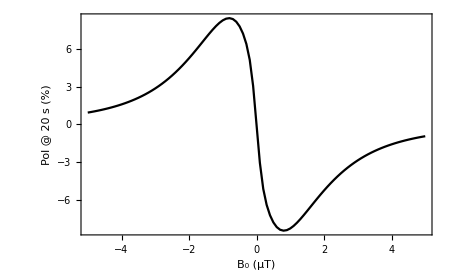

```mathematica
TimePlot[SHEATHFieldSweep[[2]],0.1,-5,Black,{"B_0 (µT)","Pol @ 20 s (%)"}]
```

```mathematica
Range[-5,5,0.1][[FindMax[SHEATHFieldSweep[[2]]]]]
```

-0.8

```mathematica
UploadDataToCSV[charger,"/Users/rajivraman/Downloads/SABRE_SHEATH_Dataset.csv"]
```

Uploaded data to CSV.

```mathematica
Δt=2.5;
kNkHSweep=ParallelTable[Table[
{-0.8,kN,kH,0.05,0,60000,2.5,Last@DMExFR2DualHv[
{U1[-0.8,Δt]},(*propagators for isomer 1 [Bz,Bx,By,dt]*)
{U2[-0.8,Δt]},(*propagators for isomer 2*)
{UF[-0.8,Δt]},(*propagators for free species*)
ρ0,ρF0(*initial conditions for bound and free species*),
kN(*target dissociation rate*),kH(*pH2 association rate*),
1/20(*[Ir]/[L]*),0(*[Ir]/[H2], flowing continuously*),
{60000/Δt}(*number of simulation steps, T/Δt*),{Δt}(*Δt*),1]}
,{kH,0.25,kN-0.5,0.5}],{kN,1,30,2}];
```

```mathematica
injection1=Flatten[kNkHSweep,1];
```

```mathematica
UploadDataToCSV[injection1,"/Users/rajivraman/Downloads/SABRE_SHEATH_Dataset.csv"]
```

Uploaded data to CSV.

```mathematica
Δt=2.5;
concentrationSweep=ParallelTable[Table[
{-0.8,16,2,0.05,0,60000,2.5,Last@DMExFR2DualHv[
{U1[-0.8,Δt]},(*propagators for isomer 1 [Bz,Bx,By,dt]*)
{U2[-0.8,Δt]},(*propagators for isomer 2*)
{UF[-0.8,Δt]},(*propagators for free species*)
ρ0,ρF0(*initial conditions for bound and free species*),
16(*target dissociation rate*),2(*pH2 association rate*),
IrL(*[Ir]/[L]*),IrH2(*[Ir]/[H2], flowing continuously*),
{60000/Δt}(*number of simulation steps, T/Δt*),{Δt}(*Δt*),1]}
,{IrL,0.01,0.5,0.02}],{IrH2,0,0.2,0.02}];
```

```mathematica
injection2=Flatten[concentrationSweep,1];
```

```mathematica
concTable=Flatten[Table[Table[{IrL,IrH2},{IrL,0.01,0.5,0.02}],{IrH2,0,0.2,0.02}],1];
```

```mathematica
fixedInjection2={injection2ᵀ[[1]],injection2ᵀ[[2]],injection2ᵀ[[3]],concTableᵀ[[1]],concTableᵀ[[2]],injection2ᵀ[[6]],injection2ᵀ[[7]],injection2ᵀ[[8]]}ᵀ;
```

```mathematica
UploadDataToCSV[fixedInjection2,"/Users/rajivraman/Downloads/SABRE_SHEATH_Dataset.csv"]
```

Uploaded data to CSV.

```mathematica
Δt=2.5;
runtimeB0Sweep=ParallelTable[Table[
{B0,16,2,0.05,0,runtime,2.5,Last@DMExFR2DualHv[
{U1[B0,Δt]},(*propagators for isomer 1 [Bz,Bx,By,dt]*)
{U2[B0,Δt]},(*propagators for isomer 2*)
{UF[B0,Δt]},(*propagators for free species*)
ρ0,ρF0(*initial conditions for bound and free species*),
16(*target dissociation rate*),2(*pH2 association rate*),
1/20(*[Ir]/[L]*),0(*[Ir]/[H2], flowing continuously*),
{runtime/Δt}(*number of simulation steps, T/Δt*),{Δt}(*Δt*),1]}
,{runtime,1000,60000,4000}],{B0,-5,5,0.5}];
```

```mathematica
injection3=Flatten[runtimeB0Sweep,1];
```

```mathematica
UploadDataToCSV[injection3,"/Users/rajivraman/Downloads/SABRE_SHEATH_Dataset.csv"]
```

Uploaded data to CSV.

```mathematica
runtimeDTSweep=ParallelTable[Table[
{-0.8,16,2,0.05,0,runtime,dt,Last@DMExFR2DualHv[
{U1[-0.8,dt]},(*propagators for isomer 1 [Bz,Bx,By,dt]*)
{U2[-0.8,dt]},(*propagators for isomer 2*)
{UF[-0.8,dt]},(*propagators for free species*)
ρ0,ρF0(*initial conditions for bound and free species*),
16(*target dissociation rate*),2(*pH2 association rate*),
1/20(*[Ir]/[L]*),0(*[Ir]/[H2], flowing continuously*),
{runtime/dt}(*number of simulation steps, T/Δt*),{dt}(*Δt*),1]}
,{runtime,1000,60000,4000}],{dt,{0.5,1,2.5,5,10,20,50,100}}];
```

```mathematica
injection4=Flatten[runtimeDTSweep,1];
```

```mathematica
UploadDataToCSV[injection4,"/Users/rajivraman/Downloads/SABRE_SHEATH_Dataset.csv"]
```

Uploaded data to CSV.

```mathematica
runtimeDTSweep2=ParallelTable[Table[
{-0.8,16,2,0.05,0,runtime,dt,Last@DMExFR2DualHv[
{U1[-0.8,dt]},(*propagators for isomer 1 [Bz,Bx,By,dt]*)
{U2[-0.8,dt]},(*propagators for isomer 2*)
{UF[-0.8,dt]},(*propagators for free species*)
ρ0,ρF0(*initial conditions for bound and free species*),
16(*target dissociation rate*),2(*pH2 association rate*),
1/20(*[Ir]/[L]*),0(*[Ir]/[H2], flowing continuously*),
{runtime/dt}(*number of simulation steps, T/Δt*),{dt}(*Δt*),1]}
,{runtime,1000,60000,4000}],{dt,{0.25,150,200,250,300}}];
```

```mathematica
injection5=Flatten[runtimeDTSweep2,1];
```

```mathematica
UploadDataToCSV[injection5,"/Users/rajivraman/Downloads/SABRE_SHEATH_Dataset.csv"]
```

Uploaded data to CSV.

## CORE

This entire cell should be evaluated prior to any calculation made in the notebook. If only specific components are required, each module may also be loaded individually, though the runtime difference is minimal.

## Rajiv’s Toolbox

```mathematica
FindMax[list_]:=Position[list,Max[list]][[1,1]];
```

FSPlot takes a raw DMExFR2 field sweep from minField to maxField at fieldStep, and it returns a graph of the field profile.

```mathematica
FSPlot[rawData_,minField_,maxField_,fieldStep_]:=TracePlot[{Range[minField,maxField,fieldStep],rawData}ᵀ,Black,{"B_z (µT)","Polarization (%)"},PlotRange->All];
```

StandardFS runs a SABRE-SHEATH field sweep with no pulsing and typical parameters (k_N=16 s^-1, k_H=2 s^-1, [Ir]:[S] = 1:20,[Ir]:[H] = 0).

```mathematica
StandardFS[runtime_, timeStep_,minField_, maxField_, fieldStep_]:=Module[{TR = runtime,dt=timeStep,min = minField, max = maxField, step= fieldStep, output},
output=Table[Last@DMExFR2DualHv[
{U1[B0,0,0,dt]},(*propagators for isomer 1 [Bz,Bx,By,dt]*)
{U2[B0,0,0,dt]},(*propagators for isomer 2*)
{UF[B0,0,0,dt]},(*propagators for free species*)
ρ0,ρF0(*initial conditions for bound and free species*),
16(*target dissociation rate*),2(*pH2 association rate*),
1/20(*[Ir]/[L]*),0(*[Ir]/[H2], flowing continuously*),
{TR/dt}(*number of simulation steps, T/Δt*),{dt}(*Δt*),1],{B0,-min,max,step}];
]
```

XZStrikeFS runs a SABRE-SHEATH field sweep with XZ and YZ pulsing (as suggested by Warren) and typical parameters (k_N=16 s^-1, k_H=2 s^-1, [Ir]:[S] = 1:20,[Ir]:[H] = 0).

```mathematica
XZStrikeFS[JSYNC_,runtime_,pulseDur_ ,pulseStep_,delayStep_,minField_, maxField_, fieldStep_]:=Module[{J=JSYNC,TR = runtime,PD=pulseDur,ps=pulseStep,ds=delayStep,min = minField, max = maxField, step= fieldStep, τ,PP,dt,DT,output},
τ=1/(2*J)*1000;
PP= π/(γH*2π*PD*Sqrt[2]*10^-3);
dt=ps;
DT=ds;
output=ParallelTable[Last@DMExFR2DualHv[
{U1[B0,0,0,DT],U1[PP,PP,0,dt],U1[PP,-PP,0,dt],U1[B0,0,0,DT],U1[PP,0,PP,dt],U1[PP,0,-PP,dt],U1[B0,0,0,DT],U1[PP,PP,0,dt],U1[PP,-PP,0,dt],U1[B0,0,0,DT],U1[PP,0,PP,dt],U1[PP,0,-PP,dt],U1[PP,-PP,0,dt],U1[PP,PP,0,dt],U1[B0,0,0,DT],U1[PP,0,-PP,dt],U1[PP,0,PP,dt],U1[B0,0,0,DT],U1[PP,-PP,0,dt],U1[PP,PP,0,dt],U1[B0,0,0,DT],U1[PP,0,-PP,dt],U1[PP,0,PP,dt],U1[PP,-PP,0,dt],U1[PP,PP,0,dt],U1[B0,0,0,DT],U1[PP,0,-PP,dt],U1[PP,0,PP,dt],U1[B0,0,0,DT],U1[PP,-PP,0,dt],U1[PP,PP,0,dt],U1[B0,0,0,DT],U1[PP,0,-PP,dt],U1[PP,0,PP,dt],U1[PP,PP,0,dt],U1[PP,-PP,0,dt],U1[B0,0,0,DT],U1[PP,0,PP,dt],U1[PP,0,-PP,dt],U1[B0,0,0,DT],U1[PP,PP,0,dt],U1[PP,-PP,0,dt],U1[B0,0,0,DT],U1[PP,0,PP,dt],U1[PP,0,-PP,dt]},(*propagators for isomer 1[Bz,Bx,By,dt]*){U2[B0,0,0,DT],U2[PP,PP,0,dt],U2[PP,-PP,0,dt],U2[B0,0,0,DT],U2[PP,0,PP,dt],U2[PP,0,-PP,dt],U2[B0,0,0,DT],U2[PP,PP,0,dt],U2[PP,-PP,0,dt],U2[B0,0,0,DT],U2[PP,0,PP,dt],U2[PP,0,-PP,dt],U2[PP,-PP,0,dt],U2[PP,PP,0,dt],U2[B0,0,0,DT],U2[PP,0,-PP,dt],U2[PP,0,PP,dt],U2[B0,0,0,DT],U2[PP,-PP,0,dt],U2[PP,PP,0,dt],U2[B0,0,0,DT],U2[PP,0,-PP,dt],U2[PP,0,PP,dt],U2[PP,-PP,0,dt],U2[PP,PP,0,dt],U2[B0,0,0,DT],U2[PP,0,-PP,dt],U2[PP,0,PP,dt],U2[B0,0,0,DT],U2[PP,-PP,0,dt],U2[PP,PP,0,dt],U2[B0,0,0,DT],U2[PP,0,-PP,dt],U2[PP,0,PP,dt],U2[PP,PP,0,dt],U2[PP,-PP,0,dt],U2[B0,0,0,DT],U2[PP,0,PP,dt],U2[PP,0,-PP,dt],U2[B0,0,0,DT],U2[PP,PP,0,dt],U2[PP,-PP,0,dt],U2[B0,0,0,DT],U2[PP,0,PP,dt],U2[PP,0,-PP,dt]},(*propagators for isomer 2*){UF[B0,0,0,DT],UF[PP,PP,0,dt],UF[PP,-PP,0,dt],UF[B0,0,0,DT],UF[PP,0,PP,dt],UF[PP,0,-PP,dt],UF[B0,0,0,DT],UF[PP,PP,0,dt],UF[PP,-PP,0,dt],UF[B0,0,0,DT],UF[PP,0,PP,dt],UF[PP,0,-PP,dt],UF[PP,-PP,0,dt],UF[PP,PP,0,dt],UF[B0,0,0,DT],UF[PP,0,-PP,dt],UF[PP,0,PP,dt],UF[B0,0,0,DT],UF[PP,-PP,0,dt],UF[PP,PP,0,dt],UF[B0,0,0,DT],UF[PP,0,-PP,dt],UF[PP,0,PP,dt],UF[PP,-PP,0,dt],UF[PP,PP,0,dt],UF[B0,0,0,DT],UF[PP,0,-PP,dt],UF[PP,0,PP,dt],UF[B0,0,0,DT],UF[PP,-PP,0,dt],UF[PP,PP,0,dt],UF[B0,0,0,DT],UF[PP,0,-PP,dt],UF[PP,0,PP,dt],UF[PP,PP,0,dt],UF[PP,-PP,0,dt],UF[B0,0,0,DT],UF[PP,0,PP,dt],UF[PP,0,-PP,dt],UF[B0,0,0,DT],UF[PP,PP,0,dt],UF[PP,-PP,0,dt],UF[B0,0,0,DT],UF[PP,0,PP,dt],UF[PP,0,-PP,dt]},(*propagators for free species*)
ρ0,ρF0(*initial conditions for bound and free species*),
16(*target dissociation rate*),2(*pH2 association rate*),
1/20(*[Ir]/[L]*),0(*[Ir]/[H2], flowing continuously*),
{τ/DT,PD/dt,PD/dt,(τ/4)/DT,PD/dt,PD/dt,(τ/4)/DT,PD/dt,PD/dt,(τ/4)/DT,PD/dt,PD/dt,PD/dt,PD/dt,(τ/4)/DT,PD/dt,PD/dt,(τ/4)/DT,PD/dt,PD/dt,(τ/4)/DT,PD/dt,PD/dt,PD/dt,PD/dt,(τ/4)/DT,PD/dt,PD/dt,(τ/4)/DT,PD/dt,PD/dt,(τ/4)/DT,PD/dt,PD/dt,PD/dt,PD/dt,(τ/4)/DT,PD/dt,PD/dt,(τ/4)/DT,PD/dt,PD/dt,(τ/4)/DT,PD/dt,PD/dt}(*number of simulation steps, T/Δt*),{DT,dt,dt,DT,dt,dt,DT,dt,dt,DT,dt,dt,dt,dt,DT,dt,dt,DT,dt,dt,DT,dt,dt,dt,dt,DT,dt,dt,DT,dt,dt,DT,dt,dt,dt,dt,DT,dt,dt,DT,dt,dt,DT,dt,dt}(*Δt*),Round[TR/(32*PD+4*τ)]],{B0,-min,max,step}]
]
```

StandardOPT runs a standard SABRE-SHEATH field sweep and uses the optimal field to trace polarization over a specified runtime at that field.

```mathematica
StandardOPT[runtime_, timeStep_,minField_, maxField_, fieldStep_]:=Module[{TR = runtime,dt=timeStep,min = minField, max = maxField, step= fieldStep,raw,B0, output},
raw=StandardFS[TR,dt,min,max,step];
B0=Range[-min,max,step][[FindMax[raw]]];
output=DMExFR2DualHv[
{U1[B0,0,0,dt]},(*propagators for isomer 1 [Bz,Bx,By,dt]*)
{U2[B0,0,0,dt]},(*propagators for isomer 2*)
{UF[B0,0,0,dt]},(*propagators for free species*)
ρ0,ρF0(*initial conditions for bound and free species*),
16(*target dissociation rate*),2(*pH2 association rate*),
1/20(*[Ir]/[L]*),0(*[Ir]/[H2], flowing continuously*),
{TR/dt}(*number of simulation steps, T/Δt*),{dt}(*Δt*),1]
]
```

```mathematica
JModStandardOPT[runtime_, timeStep_,minField_, maxField_, fieldStep_,Jcoupling_]:=Module[{J=Jcoupling,TR = runtime,dt=timeStep,min = minField, max = maxField, step= fieldStep,raw,B0, output},
raw=StandardFS[TR,dt,min,max,step];
B0=Range[-min,max,step][[FindMax[raw]]];
output={B0,Last@DMExFR2DualHv[
{U1[J,B0,0,0,dt]},(*propagators for isomer 1 [Bz,Bx,By,dt]*)
{U2[J,B0,0,0,dt]},(*propagators for isomer 2*)
{UF[J,B0,0,0,dt]},(*propagators for free species*)
ρ0,ρF0(*initial conditions for bound and free species*),
16(*target dissociation rate*),2(*pH2 association rate*),
1/20(*[Ir]/[L]*),0(*[Ir]/[H2], flowing continuously*),
{TR/dt}(*number of simulation steps, T/Δt*),{dt}(*Δt*),1]}
]
```

XZStrikeOPT runs an XZ-pulsed field sweep and uses the optimal field to trace polarization over a specified runtime at that field.

```mathematica
XZStrikeOPT[JSYNC_,runtime_,pulseDur_ ,pulseStep_,delayStep_,minField_, maxField_, fieldStep_]:=Module[{J=JSYNC,TR = runtime,PD=pulseDur,ps=pulseStep,ds=delayStep,min = minField, max = maxField, step= fieldStep, τ,PP,dt,DT,raw,B0,output},
τ=1/(2*J)*1000;
PP= π/(γH*2π*PD*Sqrt[2]*10^-3);
dt=ps;
DT=ds;
raw=XZStrikeFS[J,TR,PD,ps,ds,min,max,step];
B0=Range[-min,max,step][[FindMax[raw]]];
output=DMExFR2DualHv[
{U1[B0,0,0,DT],U1[PP,PP,0,dt],U1[PP,-PP,0,dt],U1[B0,0,0,DT],U1[PP,0,PP,dt],U1[PP,0,-PP,dt],U1[B0,0,0,DT],U1[PP,PP,0,dt],U1[PP,-PP,0,dt],U1[B0,0,0,DT],U1[PP,0,PP,dt],U1[PP,0,-PP,dt],U1[PP,-PP,0,dt],U1[PP,PP,0,dt],U1[B0,0,0,DT],U1[PP,0,-PP,dt],U1[PP,0,PP,dt],U1[B0,0,0,DT],U1[PP,-PP,0,dt],U1[PP,PP,0,dt],U1[B0,0,0,DT],U1[PP,0,-PP,dt],U1[PP,0,PP,dt],U1[PP,-PP,0,dt],U1[PP,PP,0,dt],U1[B0,0,0,DT],U1[PP,0,-PP,dt],U1[PP,0,PP,dt],U1[B0,0,0,DT],U1[PP,-PP,0,dt],U1[PP,PP,0,dt],U1[B0,0,0,DT],U1[PP,0,-PP,dt],U1[PP,0,PP,dt],U1[PP,PP,0,dt],U1[PP,-PP,0,dt],U1[B0,0,0,DT],U1[PP,0,PP,dt],U1[PP,0,-PP,dt],U1[B0,0,0,DT],U1[PP,PP,0,dt],U1[PP,-PP,0,dt],U1[B0,0,0,DT],U1[PP,0,PP,dt],U1[PP,0,-PP,dt]},(*propagators for isomer 1[Bz,Bx,By,dt]*){U2[B0,0,0,DT],U2[PP,PP,0,dt],U2[PP,-PP,0,dt],U2[B0,0,0,DT],U2[PP,0,PP,dt],U2[PP,0,-PP,dt],U2[B0,0,0,DT],U2[PP,PP,0,dt],U2[PP,-PP,0,dt],U2[B0,0,0,DT],U2[PP,0,PP,dt],U2[PP,0,-PP,dt],U2[PP,-PP,0,dt],U2[PP,PP,0,dt],U2[B0,0,0,DT],U2[PP,0,-PP,dt],U2[PP,0,PP,dt],U2[B0,0,0,DT],U2[PP,-PP,0,dt],U2[PP,PP,0,dt],U2[B0,0,0,DT],U2[PP,0,-PP,dt],U2[PP,0,PP,dt],U2[PP,-PP,0,dt],U2[PP,PP,0,dt],U2[B0,0,0,DT],U2[PP,0,-PP,dt],U2[PP,0,PP,dt],U2[B0,0,0,DT],U2[PP,-PP,0,dt],U2[PP,PP,0,dt],U2[B0,0,0,DT],U2[PP,0,-PP,dt],U2[PP,0,PP,dt],U2[PP,PP,0,dt],U2[PP,-PP,0,dt],U2[B0,0,0,DT],U2[PP,0,PP,dt],U2[PP,0,-PP,dt],U2[B0,0,0,DT],U2[PP,PP,0,dt],U2[PP,-PP,0,dt],U2[B0,0,0,DT],U2[PP,0,PP,dt],U2[PP,0,-PP,dt]},(*propagators for isomer 2*){UF[B0,0,0,DT],UF[PP,PP,0,dt],UF[PP,-PP,0,dt],UF[B0,0,0,DT],UF[PP,0,PP,dt],UF[PP,0,-PP,dt],UF[B0,0,0,DT],UF[PP,PP,0,dt],UF[PP,-PP,0,dt],UF[B0,0,0,DT],UF[PP,0,PP,dt],UF[PP,0,-PP,dt],UF[PP,-PP,0,dt],UF[PP,PP,0,dt],UF[B0,0,0,DT],UF[PP,0,-PP,dt],UF[PP,0,PP,dt],UF[B0,0,0,DT],UF[PP,-PP,0,dt],UF[PP,PP,0,dt],UF[B0,0,0,DT],UF[PP,0,-PP,dt],UF[PP,0,PP,dt],UF[PP,-PP,0,dt],UF[PP,PP,0,dt],UF[B0,0,0,DT],UF[PP,0,-PP,dt],UF[PP,0,PP,dt],UF[B0,0,0,DT],UF[PP,-PP,0,dt],UF[PP,PP,0,dt],UF[B0,0,0,DT],UF[PP,0,-PP,dt],UF[PP,0,PP,dt],UF[PP,PP,0,dt],UF[PP,-PP,0,dt],UF[B0,0,0,DT],UF[PP,0,PP,dt],UF[PP,0,-PP,dt],UF[B0,0,0,DT],UF[PP,PP,0,dt],UF[PP,-PP,0,dt],UF[B0,0,0,DT],UF[PP,0,PP,dt],UF[PP,0,-PP,dt]},(*propagators for free species*)
ρ0,ρF0(*initial conditions for bound and free species*),
16(*target dissociation rate*),2(*pH2 association rate*),
1/20(*[Ir]/[L]*),0(*[Ir]/[H2], flowing continuously*),
{τ/DT,PD/dt,PD/dt,(τ/4)/DT,PD/dt,PD/dt,(τ/4)/DT,PD/dt,PD/dt,(τ/4)/DT,PD/dt,PD/dt,PD/dt,PD/dt,(τ/4)/DT,PD/dt,PD/dt,(τ/4)/DT,PD/dt,PD/dt,(τ/4)/DT,PD/dt,PD/dt,PD/dt,PD/dt,(τ/4)/DT,PD/dt,PD/dt,(τ/4)/DT,PD/dt,PD/dt,(τ/4)/DT,PD/dt,PD/dt,PD/dt,PD/dt,(τ/4)/DT,PD/dt,PD/dt,(τ/4)/DT,PD/dt,PD/dt,(τ/4)/DT,PD/dt,PD/dt}(*number of simulation steps, T/Δt*),{DT,dt,dt,DT,dt,dt,DT,dt,dt,DT,dt,dt,dt,dt,DT,dt,dt,DT,dt,dt,DT,dt,dt,dt,dt,DT,dt,dt,DT,dt,dt,DT,dt,dt,dt,dt,DT,dt,dt,DT,dt,dt,DT,dt,dt}(*Δt*),Round[TR/(32*PD+4*τ)]]
]
```

```mathematica
Zeros[length_]:=0*Range[1,length];
```

```mathematica
OnesList[length_]:=Range[1,length]/Range[1,length];
```

```mathematica
RectFunction[leftEdge_,rightEdge_,point_]:=UnitStep[point-leftEdge]-UnitStep[point-rightEdge];
```

```mathematica
HypeTan[edgeFreq_,leftEdge_,rightEdge_,point_]:=(Tanh[edgeFreq*(point-leftEdge)]*Tanh[edgeFreq*(point-rightEdge)]);
```

```mathematica
isoU[γ_,Bx_,By_,Bz_,dt_]:=MatrixExp[2*π*I*(γ*Bx*OperatorNF[1,{1,x}]+γ*By*OperatorNF[1,{1,y}]+γ*Bz*OperatorNF[1,{1,z}])*dt*0.001];
```

```mathematica
propGen[γ_,x_,y_,z_,dt_,T_]:=Table[isoU[γ,x[[i]],y[[i]],z[[i]],dt],{i,1,T/dt}];
```

```mathematica
ZMagEval[γ_,x_,y_,z_,times_,dt_,T_]:=OneLvNSolve[propGen[γ,x,y,z,dt,T],OperatorNF[1,{1,z}],times,OperatorNF[1,{1,z}]];
```

```mathematica
Normalizer[list_]:=list/Max[Abs[list]];
```

```mathematica
XY4CosPC[period_,power_,point_]:=Module[{T=period,t=point,domain,output},
output=If[t<T∨t>3T,1-(Cos[(π*t)/T])^power,(Cos[(π*t)/T])^power-1]
];
```

```mathematica
PhaseCycle[pulse_,period_,dt_]:=Module[{stitch,times,P=period,cycledStitch,output},
stitch=Delete[Join[pulse,pulse,pulse,pulse],{{Floor[period/(dt)]},{2*Floor[period/(dt)]},{3*Floor[period/(dt)]}}];
times=Range[0,Length[stitch]*dt-dt,dt];
cycledStitch=Table[stitch[[j]]*XY4CosPC[P,12,times[[j]]],{j,1,Length[times]}];
output=cycledStitch
];
```

```mathematica
CosProduct[degree_,domain_,possibleFreqs_]:=Module[{freqs,product,output},
freqs=possibleFreqs[[1;;degree]];
product=Times@@Table[Table[Cos[freqs[[j]]*domain[[i]]],{i,1,Length[domain]}],{j,1,degree}];
output=product
];
```

```mathematica
SineMod[cycles_,period_,phase_,domain_]:=Table[Sin[(2π*cycles)/period*domain[[i]]-phase],{i,1,Length[domain]}];
```

```mathematica
PolyMod[cheb_,period_,domain_]:=Table[ChebyshevT[cheb,domain[[i]]-period/2],{i,1,Length[domain]}];
```

```mathematica
TimeAmpMod[cycles_,phase_,cheb_,period_,domain_,phaseCount_]:=Delete[If[cycles==0,OnesList[4*Length[domain]],Join@@Table[SineMod[cycles,period,phase,domain]*PolyMod[cheb,period,domain],{j,1,phaseCount}]],{{Floor[period/(domain[[2]]-domain[[1]])]},{Floor[2*period/(domain[[2]]-domain[[1]])]},{Floor[3*period/(domain[[2]]-domain[[1]])]}}];
```

```mathematica
PeriodToXY16[fullPulse_,period_,timestep_,edgeFreq_]:=Module[{P=period,dt=timestep,F=edgeFreq,delay,delayPulse,cycler,times,output},
times=Range[0,Round[(16*period)/3,dt],dt];
delay=Round[(4*period)/3,dt];
delayPulse=Zeros[delay/dt];
cycler=Table[-1*fullPulse[[j]]*HypeTan[F,0,P,times[[j]]]*HypeTan[F,3P,4P,times[[j]]],{j,1,Length[fullPulse]}];
output=Join[delayPulse,cycler]
];
```

```mathematica
OneLvNSolve[U1_,ρ0_,tf_,OP_]:=Module[{ρ1,expectationValue,j,i},
ρ1=ρ0;
expectationValue={};
For[j=1,j≤Length[tf],j++,
For[i=1,i≤tf⟦j⟧,i++,
ρ1=ConjugateTranspose[U1⟦j⟧].ρ1.U1⟦j⟧;
AppendTo[expectationValue,Chop[Tr[ρ1.OP]]];
];
];
100/Norm[OP] expectationValue
]
```

```mathematica
SoloMagnetizationTracker[shaped3DPulse_,γ_,initialDensityMatrix_,targetExpectationOperator_,timestep_]:=Module[{dt=timestep,idm=initialDensityMatrix,ExpOp=targetExpectationOperator,xChannel,yChannel,zChannel,testProps,testList,output},
xChannel=shaped3DPulse[[1]];
yChannel=shaped3DPulse[[2]];
zChannel=shaped3DPulse[[3]];
testProps=propGen[γ,xChannel,yChannel,zChannel,dt,Length[xChannel]*dt];
output=OneLvNSolve[testProps,idm,OnesList[Length[testProps]],ExpOp]
]
```

```mathematica
FinalExpVal[shaped3DPulse_,γ_,initialDensityMatrix_,targetExpectationOperator_,timestep_]:=Module[{dt=timestep,idm=initialDensityMatrix,ExpOp=targetExpectationOperator,xChannel,yChannel,zChannel,testProps,testList,hold,output},
xChannel=shaped3DPulse[[1]];
yChannel=shaped3DPulse[[2]];
zChannel=shaped3DPulse[[3]];
testProps=propGen[γ,xChannel,yChannel,zChannel,dt,Length[xChannel]*dt];
output=Last@OneLvNSolve[testProps,idm,OnesList[Length[testProps]],ExpOp]
];
```

```mathematica
OptimizedPropagation[γ_,XYZshapes_,initialDensityMatrix_,ExpOp_,timestep_,nullField_]:=Module[{dt=timestep,NF=nullField,x,y,z,idm=initialDensityMatrix,OP=ExpOp,binList,indexFinder,cleaner,cleanList,propList,hold,output},x=XYZshapes[[1]];(*B(t) applied along x-axis*)y=XYZshapes[[2]];(*B(t) applied along y-axis*)z=XYZshapes[[3]];(*B(t) applied along z-axis*)binList=Table[If[Chop[x[[j]],NF]==0&&Chop[y[[j]],NF]==0,0,1],{j,1,Length[x]}];(*binary list that toggles to 1 when Bx(t) and By(t) are both 0 under some chop threshold*)indexFinder={};(*blank list where toggled indeces will be tracked*)cleaner={};(*imperfect chops within binList can cause delays of length dt to be found in the middle of pulses-cleaner will allow us to clip out these useless indeces*)For[j=2,j<=Length[binList],j++,If[binList[[j-1]]!=binList[[j]],AppendTo[indexFinder,j]]];(*indexFinder traces all indeces where binList switches from 0 to 1 or 1 to 0*)For[j=2,j<=Length[indexFinder],j++,If[indexFinder[[j]]==indexFinder[[j-1]]+1,AppendTo[cleaner,{j-1}];
AppendTo[cleaner,{j}];]];(*cleaner picks up all delays of length dt*)cleanList=Join[{1},Delete[indexFinder,cleaner]];(*ultra-short delays embedded in pulses are deleted from indexFinder*)If[Mod[Length[cleanList],2]==1,propList=Join@@Table[Join[{isoU[γ,x[[cleanList[[j-1]]]],y[[cleanList[[j-1]]]],z[[cleanList[[j-1]]]],dt*(cleanList[[j]]-cleanList[[j-1]])]},Table[isoU[γ,x[[k]],y[[k]],z[[k]],dt],{k,cleanList[[j]],cleanList[[j+1]]-1}]],{j,2,Length[cleanList]-1,2}];(*generates an optimized list of propagators with all delays treated via one propagator each*),propList=Table[isoU[γ,x[[k]],y[[k]],z[[k]],dt],{k,1,Length[x]}];(*generates an optimized list of propagators with all delays treated via one propagator each*)];
output=OneLvNSolve[propList,idm,OnesList[Length[propList]],OP]];
```

```mathematica
FilterShapes[thres_,γ_,ListOfXShapes_,ListOfYShapes_,ListOfZFields_,timestep_]:=
Module[{dt=timestep,X=ListOfXShapes,Y=ListOfYShapes,ZF=ListOfZFields,mag,λ1,λ2,filteredXList,filteredYList,filteredZList,indexList,test,hold,output},
filteredXList={};
filteredYList={};
filteredZList={};
indexList={};
ParallelTable[
mag=OptimizedPropagation[γ,{X[[k]],Y[[k]]},ZF[[k]],OperatorNF[1,{1,z}],OperatorNF[1,{1,z}],dt,0.1];
λ1=Min[mag]/Max[mag];
λ2=(Last@mag)/Max[mag];
test=1/2*Dot[{1,1},{λ1,λ2}];
If[test>=thres,
AppendTo[filteredXList,X[[k]]];
AppendTo[filteredYList,Y[[k]]];
AppendTo[filteredZList,ZF[[k]]];
AppendTo[indexList,k];
]
,{k,1,Length[X]}];
output={filteredXList,filteredYList,filteredZList,indexList}
]
```

```mathematica
ComputeShape[γ_,XShape_,YShape_,ZShape_,timestep_]:=Module[{dt=timestep,X=XShape,Y=YShape,Z=ZShape,mag,λ1,λ2,test,hold,output},mag=OptimizedPropagation[γ,{X,Y,Z},OperatorNF[1,{1,z}],OperatorNF[1,{1,z}],dt,0.1];
If[Length[mag]>0,λ1=Min[mag]/Max[mag];
λ2=(Last@mag)/Max[mag];
test=1/2*Dot[{1,1},{λ1,λ2}];
output=test;,output=-1;];
output]
```

```mathematica
ShapeMagic[ParameterTable_,timestep_,request_]:=Module[{genP=ParameterTable,dt=timestep,req=request,freqsP,fxData,fyData,ModFx,ModFy,ifxData,ifyData,XPeriod,YPeriod,shapesX,shapesY,sliceX,sliceY,U1List,U2List,UFList,output},
freqsP=Range[-10,10,1/genP[[20]]];

fxData=Table[N[Exp[-genP[[1]]*j^2]*Exp[-genP[[7]]*Abs[j]]*Cos[genP[[3]]*j]*Exp[-2*π*I*j*genP[[5]]]],{j,freqsP}];
fyData=Table[N[Exp[-genP[[2]]*j^2]*Exp[-genP[[8]]*Abs[j]]*Cos[genP[[4]]*j]*Exp[-2*π*I*j*genP[[6]]]],{j,freqsP}];

ModFx=fxData*CosProduct[genP[[9]],freqsP,{genP[[22]],genP[[23]],genP[[24]],genP[[25]],genP[[26]]}];
ModFy=fyData*CosProduct[genP[[10]],freqsP,{genP[[27]],genP[[28]],genP[[29]],genP[[30]],genP[[31]]}];

ifxData=Sum[N[ModFx[[j]]*Exp[I*2*π*freqsP[[j]]*Range[0,4*genP[[20]],dt]]],{j,1,Length[ModFx]}];
ifyData=Sum[N[ModFy[[j]]*Exp[I*2*π*freqsP[[j]]*Range[0,4*genP[[20]],dt]]],{j,1,Length[ModFy]}];

XPeriod=Re[ifxData]*TimeAmpMod[genP[[11]],genP[[13]],genP[[15]],genP[[20]],Range[0,genP[[20]],dt],4];
YPeriod=Re[ifyData]*TimeAmpMod[genP[[12]],genP[[14]],genP[[16]],genP[[20]],Range[0,genP[[20]],dt],4];

shapesX=genP[[17]]*Normalizer[PeriodToXY16[XPeriod,genP[[20]],dt,2]];
shapesY=genP[[18]]*Normalizer[PeriodToXY16[YPeriod,genP[[20]],dt,2]];

If[req=="Graph",
output=Show[TracePlot[{Range[0,(Length[shapesX]-1)*dt,dt],shapesX}ᵀ,Red,{"t (ms)","Amplitude (µT)"},{0,(Length[shapesX]-1)*dt}],TracePlot[{Range[0,(Length[shapesY]-1)*dt,dt],shapesY}ᵀ,Blue,{"t (ms)","Amplitude (µT)"},{0,(Length[shapesX]-1)*dt}],PlotRange->All];
];

If[req=="Generate",
output={shapesX,shapesY};
];

If[req=="Pol",
output=SliceAndPolarize[shapesX,shapesY,genP[[21]],dt,20000];
];

If[req=="FullPol",
output=SliceAndPolarize[shapesX,shapesY,genP[[21]],dt,60000];
];

output
]
```

```mathematica
AddDelay[list_,duration_,dt_]:=Join[Zeros[duration/dt],list];
```

```mathematica
AddDCDelay[list_,duration_,dt_,DC_]:=Join[DC*OnesList[duration/dt],list];
```

```mathematica
SliceAndPolarize[shapeX_,shapeY_,zField_,timestep_,runtime_]:=Module[{dt=timestep,sliceX,sliceY,endSliceX,endSliceY,fullX,fullY,U1List,U2List,UFList,output},
sliceX=Partition[shapeX,Floor[2.5/dt]];
sliceY=Partition[shapeY,Floor[2.5/dt]];
endSliceX=shapeX[[Length[sliceX]*Floor[2.5/dt]+1;;]];
endSliceY=shapeY[[Length[sliceY]*Floor[2.5/dt]+1;;]];
If[Length[endSliceX]>0,
fullX=Join[sliceX,{endSliceX}];
fullY=Join[sliceY,{endSliceY}];
,
fullX=sliceX;
fullY=sliceY;
];
U1List=Table[Dot@@Table[U1[zField,fullX[[k,l]],fullY[[k,l]],dt],{l,1,Length[fullX[[k]]]}],{k,1,Length[fullX]}];
U2List=Table[Dot@@Table[U2[zField,fullX[[k,l]],fullY[[k,l]],dt],{l,1,Length[fullX[[k]]]}],{k,1,Length[fullX]}];
UFList=Table[Dot@@Table[UF[zField,fullX[[k,l]],fullY[[k,l]],dt],{l,1,Length[fullX[[k]]]}],{k,1,Length[fullX]}];
output=Last@DMExFR2DualHv[
U1List(*propagators for isomer 1*),
U2List(*propagators for isomer 2*),
UFList(*propagators for free species*),
ρ0,ρF0(*initial conditions for bound and free species*),
16(*target dissociation rate*),2(*pH2 association rate*),
1/20(*[Ir]/[L]*),0(*[Ir]/[H2], flowing continuously*),
OnesList[Length[fullX]](*number of simulation steps, T/Δt*),Table[Length[fullX[[j]]]*dt,{j,1,Length[fullX]}] (*Δt*),Round[runtime/(Length[shapeX]*dt)]]
];
```

```mathematica
ShapePolarize[shapeX_,shapeY_,shapeZ_,timestep_,runtime_]:=Module[{dt=timestep,sliceX,sliceY,sliceZ,endSliceX,endSliceY,endSliceZ,fullX,fullY,fullZ,U1List,U2List,UFList,output},
sliceX=Partition[shapeX,Floor[2.5/dt]];
sliceY=Partition[shapeY,Floor[2.5/dt]];
sliceZ=Partition[shapeZ,Floor[2.5/dt]];
endSliceX=shapeX[[Length[sliceX]*Floor[2.5/dt]+1;;]];
endSliceY=shapeY[[Length[sliceY]*Floor[2.5/dt]+1;;]];
endSliceZ=shapeZ[[Length[sliceZ]*Floor[2.5/dt]+1;;]];
If[Length[endSliceX]>0,
fullX=Join[sliceX,{endSliceX}];
fullY=Join[sliceY,{endSliceY}];
fullZ=Join[sliceZ,{endSliceZ}];
,
fullX=sliceX;
fullY=sliceY;
fullZ=sliceZ
];
U1List=Table[Dot@@Table[U1[fullZ[[k,l]],fullX[[k,l]],fullY[[k,l]],dt],{l,1,Length[fullX[[k]]]}],{k,1,Length[fullX]}];
U2List=Table[Dot@@Table[U2[fullZ[[k,l]],fullX[[k,l]],fullY[[k,l]],dt],{l,1,Length[fullX[[k]]]}],{k,1,Length[fullX]}];
UFList=Table[Dot@@Table[UF[fullZ[[k,l]],fullX[[k,l]],fullY[[k,l]],dt],{l,1,Length[fullX[[k]]]}],{k,1,Length[fullX]}];
output=Last@DMExFR2DualHv[
U1List(*propagators for isomer 1*),
U2List(*propagators for isomer 2*),
UFList(*propagators for free species*),
ρ0,ρF0(*initial conditions for bound and free species*),
16(*target dissociation rate*),2(*pH2 association rate*),
1/20(*[Ir]/[L]*),0(*[Ir]/[H2], flowing continuously*),
OnesList[Length[fullX]](*number of simulation steps, T/Δt*),Table[Length[fullX[[j]]]*dt,{j,1,Length[fullX]}] (*Δt*),Round[runtime/(Length[shapeX]*dt)]]
];
```

```mathematica
ShapePolarizeTrace[shapeX_,shapeY_,shapeZ_,timestep_,runtime_]:=Module[{dt=timestep,sliceX,sliceY,sliceZ,endSliceX,endSliceY,endSliceZ,fullX,fullY,fullZ,U1List,U2List,UFList,output},
sliceX=Partition[shapeX,Floor[2.5/dt]];
sliceY=Partition[shapeY,Floor[2.5/dt]];
sliceZ=Partition[shapeZ,Floor[2.5/dt]];
endSliceX=shapeX[[Length[sliceX]*Floor[2.5/dt]+1;;]];
endSliceY=shapeY[[Length[sliceY]*Floor[2.5/dt]+1;;]];
endSliceZ=shapeZ[[Length[sliceZ]*Floor[2.5/dt]+1;;]];
If[Length[endSliceX]>0,
fullX=Join[sliceX,{endSliceX}];
fullY=Join[sliceY,{endSliceY}];
fullZ=Join[sliceZ,{endSliceZ}];
,
fullX=sliceX;
fullY=sliceY;
fullZ=sliceZ
];
U1List=Table[Dot@@Table[U1[fullZ[[k,l]],fullX[[k,l]],fullY[[k,l]],dt],{l,1,Length[fullX[[k]]]}],{k,1,Length[fullX]}];
U2List=Table[Dot@@Table[U2[fullZ[[k,l]],fullX[[k,l]],fullY[[k,l]],dt],{l,1,Length[fullX[[k]]]}],{k,1,Length[fullX]}];
UFList=Table[Dot@@Table[UF[fullZ[[k,l]],fullX[[k,l]],fullY[[k,l]],dt],{l,1,Length[fullX[[k]]]}],{k,1,Length[fullX]}];
output=DMExFR2DualHv[
U1List(*propagators for isomer 1*),
U2List(*propagators for isomer 2*),
UFList(*propagators for free species*),
ρ0,ρF0(*initial conditions for bound and free species*),
16(*target dissociation rate*),2(*pH2 association rate*),
1/20(*[Ir]/[L]*),0(*[Ir]/[H2], flowing continuously*),
OnesList[Length[fullX]](*number of simulation steps, T/Δt*),Table[Length[fullX[[j]]]*dt,{j,1,Length[fullX]}] (*Δt*),Round[runtime/(Length[shapeX]*dt)]]
];
```

```mathematica
SmartPolTrace[shapeX_,shapeY_,zField_,timestep_,runtime_]:=Module[{dt=timestep,sliceX,sliceY,endSliceX,endSliceY,fullX,fullY,U1List,U2List,UFList,output},
sliceX=Partition[shapeX,Floor[2.5/dt]];
sliceY=Partition[shapeY,Floor[2.5/dt]];
endSliceX=shapeX[[Length[sliceX]*Floor[2.5/dt]+1;;]];
endSliceY=shapeY[[Length[sliceY]*Floor[2.5/dt]+1;;]];
If[Length[endSliceX]>0,
fullX=Join[sliceX,{endSliceX}];
fullY=Join[sliceY,{endSliceY}];
,
fullX=sliceX;
fullY=sliceY;
];
U1List=Table[Dot@@Table[U1[zField,fullX[[k,l]],fullY[[k,l]],dt],{l,1,Length[fullX[[k]]]}],{k,1,Length[fullX]}];
U2List=Table[Dot@@Table[U2[zField,fullX[[k,l]],fullY[[k,l]],dt],{l,1,Length[fullX[[k]]]}],{k,1,Length[fullX]}];
UFList=Table[Dot@@Table[UF[zField,fullX[[k,l]],fullY[[k,l]],dt],{l,1,Length[fullX[[k]]]}],{k,1,Length[fullX]}];
output=DMExFR2DualHv[
U1List(*propagators for isomer 1*),
U2List(*propagators for isomer 2*),
UFList(*propagators for free species*),
ρ0,ρF0(*initial conditions for bound and free species*),
16(*target dissociation rate*),2(*pH2 association rate*),
1/20(*[Ir]/[L]*),0(*[Ir]/[H2], flowing continuously*),
OnesList[Length[fullX]](*number of simulation steps, T/Δt*),Table[Length[fullX[[j]]]*dt,{j,1,Length[fullX]}] (*Δt*),Round[runtime/(Length[shapeX]*dt)]]
];
```

```mathematica
ResonantShapeMagic[ParameterTable_,timestep_,request_]:=Module[{genP=ParameterTable,dt=timestep,req=request,T,domain,FFx,FFy,FreqX,FreqY,GaussX,GaussY,FreqPx,GaussPx,FreqPy,GaussPy,XPeriod,YPeriod,shapesX,shapesY,output},

T=genP[[1]]; (*duration of subperiod*)
domain=Range[0,Round[T,dt],dt];

FFx=γH*Abs[genP[[2]]]-genP[[3]];
FFy=γH*Abs[genP[[2]]]-genP[[4]];

If[genP[[7]]>0,
GaussPx=Table[{genP[[10+j]],genP[[20+j]],genP[[30+j]]},{j,1,genP[[7]]}];
GaussX=GaussAmpMod[GaussPx,T,dt];
,
GaussX=OnesList[Length[domain]];
];

If[genP[[8]]>0,
GaussPy=Table[{genP[[15+j]],genP[[25+j]],genP[[35+j]]},{j,1,genP[[8]]}];
GaussY=GaussAmpMod[GaussPy,T,dt];
,
GaussY=OnesList[Length[domain]];
];

XPeriod=Force[GaussX*Table[Sin[2π*FFx*j*0.001-genP[[5]]],{j,domain}],genP[[9]]];
YPeriod=Force[GaussY*Table[Sin[2π*FFy*j*0.001-genP[[6]]],{j,domain}],genP[[10]]];

shapesX=AddDelay[PhaseCycle[XPeriod,T,dt],Round[(4*T)/3,dt],dt];
shapesY=AddDelay[PhaseCycle[YPeriod,T,dt],Round[(4*T)/3,dt],dt];

If[req=="Graph",
output=Show[TracePlot[{Range[0,(Length[XPeriod]-1)*dt,dt],XPeriod}ᵀ,Red,{"t (ms)","Amplitude (µT)"},{0,(Length[XPeriod]-1)*dt}],TracePlot[{Range[0,(Length[YPeriod]-1)*dt,dt],YPeriod}ᵀ,Blue,{"t (ms)","Amplitude (µT)"},{0,(Length[YPeriod]-1)*dt}],PlotRange->All];
];

If[req=="FullGraph",
output=Show[TracePlot[{Range[0,(Length[shapesX]-1)*dt,dt],shapesX}ᵀ,Red,{"t (ms)","Amplitude (µT)"},{0,(Length[shapesX]-1)*dt}],TracePlot[{Range[0,(Length[shapesY]-1)*dt,dt],shapesY}ᵀ,Blue,{"t (ms)","Amplitude (µT)"},{0,(Length[shapesX]-1)*dt}],PlotRange->All];
];

If[req=="Generate",
output={shapesX,shapesY};
];

If[req=="Subperiod",
output={XPeriod,YPeriod};
];

If[req=="Envelope",
output={PhaseCycle[Force[GaussX,genP[[9]]],T,dt][[1;;Round[T/dt]]],PhaseCycle[Force[GaussY,genP[[10]]],T,dt][[1;;Round[T/dt]]]};
];

If[req=="ShortPol",
output=SliceAndPolarize[shapesX,shapesY,genP[[2]],dt,2000];
];

If[req=="Pol",
output=SliceAndPolarize[shapesX,shapesY,genP[[2]],dt,20000];
];

If[req=="FullPol",
output=SliceAndPolarize[shapesX,shapesY,genP[[2]],dt,60000];
];

If[req=="FullPolTrace",
output=TracePlot[SmartPolTrace[shapesX,shapesY,genP[[2]],dt,60000],Black,{"t (s)","Polarization (%)"},{0.001,60}];
];

If[req=="FullPolData",
output=SmartPolTrace[shapesX,shapesY,genP[[2]],dt,60000];
];

output
];
```

```mathematica
TimePlot[data_,dt_,start_,color_,axes_]:=TracePlot[{Range[start,start+(Length[data]-1)*dt,dt],data}ᵀ,color,axes,PlotRange->All];
```

```mathematica
DashedPlot[data_,dt_,start_,color_,axes_]:=TracePlot[{Range[start,start+(Length[data]-1)*dt,dt],data}ᵀ,{color,Dashed},axes,PlotRange->All];
```

```mathematica
DiscreteTimePlot[data_,dt_,start_,color_,axes_]:=PointPlot[{Range[start,start+(Length[data]-1)*dt,dt],data}ᵀ,color,axes,PlotRange->All];
```

```mathematica
Gaussian[width_, height_,center_, xVal_]:=height*Exp[-1*width*(xVal-center)^2];
```

```mathematica
GaussianPulse[width_,height_, center_,period_,step_]:=
Module[{W = width,H = height,C=center,T=period,dt = step,output},
output = Table[Gaussian[W,H,C,i],{i,0,Round[T,dt],dt}]
]
```

```mathematica
GaussAmpMod[parameters_,period_,timestep_]:=Module[{P=parameters,T=period,dt=timestep,output},
output=Sum[GaussianPulse[P[[i,1]],P[[i,2]],P[[i,3]],Round[T,dt],dt],{i,1,Length[P]}]
]
```

```mathematica
BuildFreqs[parameters_,fundamentalFrequency_,period_,timestep_]:=Module[{P=parameters,F=fundamentalFrequency,T=period,dt=timestep,base,output},
output=Sum[Table[P[[j,1]]*Sin[2π*F*(j+1)*i-P[[j,2]]],{i,0,Round[T,dt],dt}],{j,1,Length[P]}]
]
```

```mathematica
Force[signal_,power_]:=Normalizer[signal]*power;
```

```mathematica
Filter[list_,threshold_, request_]:=Module[{L=list,T=threshold,fL,fI,req=request,output},
fL={};
fI={};
For[i=1,i<=Length[L],i++,
If[L[[i]]>T,
AppendTo[fL,L[[i]]];
AppendTo[fI,i];
];
];
If[req=="Element",output=fL;];
If[req=="Index",output=fI;];
output
];
```

```mathematica
RSMAverageHamiltonian[parameters_,timestep_,auxiliaryJ_,channelRequest_,delayRequest_]:=Module[{P=parameters,dt=timestep,CR=channelRequest,DR=delayRequest,θ,νN,νH,J=auxiliaryJ,I,A,B,C,output},
If[CR=="X",
θ=(180*γH*Total[ResonantShapeMagic[P,dt,"Envelope"][[1]]]*dt)/1000; (*degrees*)
νN=γN*Abs[P[[2]]]-(γH*Abs[P[[2]]]-P[[3]]);(*Hz*)
νH=P[[3]]; (*Hz*)
];
If[CR=="Y",
θ=(180*γH*Total[ResonantShapeMagic[P,dt,"Envelope"][[2]]]*dt)/1000; (*degrees*)
νN=γN*Abs[P[[2]]]-(γH*Abs[P[[2]]]-P[[4]]);(*Hz*)
νH=P[[4]]; (*Hz*)
];
I=(Sin[2θ]-Sin[θ])/θ;
A=νN;
If[DR=="No Delay",
B=νH*I;
C=J*I;
];
If[DR=="With Delay",
B=(νH*(3I+1))/4;
C=(J*(3I+1))/4;
];
output=StringForm["`1` S_z + `2` I_z + `3` I_zS_z",Round[A,0.0001],Round[B,0.0001],Round[C,0.0001]]
];
```

```mathematica
CustomDelayRSM[ParameterTable_,timestep_,delay_,request_]:=Module[{genP=ParameterTable,dt=timestep,req=request,D=delay,T,domain,FFx,FFy,FreqX,FreqY,GaussX,GaussY,FreqPx,GaussPx,FreqPy,GaussPy,XPeriod,YPeriod,shapesX,shapesY,output},

T=genP[[1]]; (*duration of subperiod*)
domain=Range[0,Round[T,dt],dt];

FFx=γH*Abs[genP[[2]]]-genP[[3]];
FFy=γH*Abs[genP[[2]]]-genP[[4]];

If[genP[[7]]>0,
GaussPx=Table[{genP[[10+j]],genP[[20+j]],genP[[30+j]]},{j,1,genP[[7]]}];
GaussX=GaussAmpMod[GaussPx,T,dt];
,
GaussX=OnesList[Length[domain]];
];

If[genP[[8]]>0,
GaussPy=Table[{genP[[15+j]],genP[[25+j]],genP[[35+j]]},{j,1,genP[[8]]}];
GaussY=GaussAmpMod[GaussPy,T,dt];
,
GaussY=OnesList[Length[domain]];
];

XPeriod=Force[GaussX*Table[Sin[2π*FFx*j*0.001-genP[[5]]],{j,domain}],genP[[9]]];
YPeriod=Force[GaussY*Table[Sin[2π*FFy*j*0.001-genP[[6]]],{j,domain}],genP[[10]]];

shapesX=AddDelay[PhaseCycle[XPeriod,T,dt],Round[D,dt],dt];
shapesY=AddDelay[PhaseCycle[YPeriod,T,dt],Round[D,dt],dt];

If[req=="Graph",
output=Show[TracePlot[{Range[0,(Length[XPeriod]-1)*dt,dt],XPeriod}ᵀ,Red,{"t (ms)","Amplitude (µT)"},{0,(Length[XPeriod]-1)*dt}],TracePlot[{Range[0,(Length[YPeriod]-1)*dt,dt],YPeriod}ᵀ,Blue,{"t (ms)","Amplitude (µT)"},{0,(Length[YPeriod]-1)*dt}],PlotRange->All];
];

If[req=="FullGraph",
output=Show[TracePlot[{Range[0,(Length[shapesX]-1)*dt,dt],shapesX}ᵀ,Red,{"t (ms)","Amplitude (µT)"},{0,(Length[shapesX]-1)*dt}],TracePlot[{Range[0,(Length[shapesY]-1)*dt,dt],shapesY}ᵀ,Blue,{"t (ms)","Amplitude (µT)"},{0,(Length[shapesX]-1)*dt}],PlotRange->All];
];

If[req=="Generate",
output={shapesX,shapesY};
];

If[req=="Subperiod",
output={XPeriod,YPeriod};
];

If[req=="Envelope",
output={PhaseCycle[Force[GaussX,genP[[9]]],T,dt][[1;;Round[T/dt]]],PhaseCycle[Force[GaussY,genP[[10]]],T,dt][[1;;Round[T/dt]]]};
];

If[req=="ShortPol",
output=SliceAndPolarize[shapesX,shapesY,genP[[2]],dt,2000];
];

If[req=="Pol",
output=SliceAndPolarize[shapesX,shapesY,genP[[2]],dt,20000];
];

If[req=="FullPol",
output=SliceAndPolarize[shapesX,shapesY,genP[[2]],dt,60000];
];

If[req=="FullPolTrace",
output=TracePlot[SmartPolTrace[shapesX,shapesY,genP[[2]],dt,60000],Black,{"t (s)","Polarization (%)"},{0.001,60}];
];

If[req=="FullPolData",
output=SmartPolTrace[shapesX,shapesY,genP[[2]],dt,60000];
];

output
];
```

```mathematica
ExModPolarize[shapeX_,shapeY_,zField_,kN_,kH_,timestep_,runtime_]:=Module[{dt=timestep,sliceX,sliceY,endSliceX,endSliceY,fullX,fullY,U1List,U2List,UFList,output},
sliceX=Partition[shapeX,Floor[2.5/dt]];
sliceY=Partition[shapeY,Floor[2.5/dt]];
endSliceX=shapeX[[Length[sliceX]*Floor[2.5/dt]+1;;]];
endSliceY=shapeY[[Length[sliceY]*Floor[2.5/dt]+1;;]];
If[Length[endSliceX]>0,
fullX=Join[sliceX,{endSliceX}];
fullY=Join[sliceY,{endSliceY}];
,
fullX=sliceX;
fullY=sliceY;
];
U1List=Table[Dot@@Table[U1[zField,fullX[[k,l]],fullY[[k,l]],dt],{l,1,Length[fullX[[k]]]}],{k,1,Length[fullX]}];
U2List=Table[Dot@@Table[U2[zField,fullX[[k,l]],fullY[[k,l]],dt],{l,1,Length[fullX[[k]]]}],{k,1,Length[fullX]}];
UFList=Table[Dot@@Table[UF[zField,fullX[[k,l]],fullY[[k,l]],dt],{l,1,Length[fullX[[k]]]}],{k,1,Length[fullX]}];
output=Last@DMExFR2DualHv[
U1List(*propagators for isomer 1*),
U2List(*propagators for isomer 2*),
UFList(*propagators for free species*),
ρ0,ρF0(*initial conditions for bound and free species*),
kN(*target dissociation rate*),kH(*pH2 association rate*),
1/20(*[Ir]/[L]*),0(*[Ir]/[H2], flowing continuously*),
OnesList[Length[fullX]](*number of simulation steps, T/Δt*),Table[Length[fullX[[j]]]*dt,{j,1,Length[fullX]}] (*Δt*),Round[runtime/(Length[shapeX]*dt)]]
];
```

```mathematica
ModXY4CosPC[period_,power_,point_,mod_]:=Module[{T=period,t=point,domain,output},
output=If[t<T∨t>3T,1-(Cos[(π*t)/T])^power,mod*((Cos[(π*t)/T])^power-1)]
];
```

```mathematica
ModPhaseCycle[pulse_,period_,dt_, mod_]:=Module[{stitch,times,P=period,cycledStitch,output},
stitch=Delete[Join[pulse,pulse,pulse,pulse],{{Floor[period/(dt)]},{2*Floor[period/(dt)]},{3*Floor[period/(dt)]}}];
times=Range[0,Length[stitch]*dt-dt,dt];
cycledStitch=Table[stitch[[j]]*ModXY4CosPC[P,12,times[[j]],mod],{j,1,Length[times]}];
output=cycledStitch
];
```

```mathematica
CustomCycleRSM[ParameterTable_,scaleBar_,timestep_,request_]:=Module[{genP=ParameterTable,dt=timestep,A=scaleBar,req=request,T,domain,FFx,FFy,FreqX,FreqY,GaussX,GaussY,FreqPx,GaussPx,FreqPy,GaussPy,XPeriod,YPeriod,shapesX,shapesY,output},

T=genP[[1]]; (*duration of subperiod*)
domain=Range[0,Round[T,dt],dt];

FFx=γH*Abs[genP[[2]]]-genP[[3]];
FFy=γH*Abs[genP[[2]]]-genP[[4]];

If[genP[[7]]>0,
GaussPx=Table[{genP[[10+j]],genP[[20+j]],genP[[30+j]]},{j,1,genP[[7]]}];
GaussX=GaussAmpMod[GaussPx,T,dt];
,
GaussX=OnesList[Length[domain]];
];

If[genP[[8]]>0,
GaussPy=Table[{genP[[15+j]],genP[[25+j]],genP[[35+j]]},{j,1,genP[[8]]}];
GaussY=GaussAmpMod[GaussPy,T,dt];
,
GaussY=OnesList[Length[domain]];
];

XPeriod=Force[GaussX*Table[Sin[2π*FFx*j*0.001-genP[[5]]],{j,domain}],genP[[9]]];
YPeriod=Force[GaussY*Table[Sin[2π*FFy*j*0.001-genP[[6]]],{j,domain}],genP[[10]]];

shapesX=AddDelay[ModPhaseCycle[XPeriod,T,dt,A],Round[(4*T)/3,dt],dt];
shapesY=AddDelay[ModPhaseCycle[YPeriod,T,dt,A],Round[(4*T)/3,dt],dt];

If[req=="Graph",
output=Show[TracePlot[{Range[0,(Length[XPeriod]-1)*dt,dt],XPeriod}ᵀ,Red,{"t (ms)","Amplitude (µT)"},{0,(Length[XPeriod]-1)*dt}],TracePlot[{Range[0,(Length[YPeriod]-1)*dt,dt],YPeriod}ᵀ,Blue,{"t (ms)","Amplitude (µT)"},{0,(Length[YPeriod]-1)*dt}],PlotRange->All];
];

If[req=="FullGraph",
output=Show[TracePlot[{Range[0,(Length[shapesX]-1)*dt,dt],shapesX}ᵀ,Red,{"t (ms)","Amplitude (µT)"},{0,(Length[shapesX]-1)*dt}],TracePlot[{Range[0,(Length[shapesY]-1)*dt,dt],shapesY}ᵀ,Blue,{"t (ms)","Amplitude (µT)"},{0,(Length[shapesX]-1)*dt}],PlotRange->All];
];

If[req=="Generate",
output={shapesX,shapesY};
];

If[req=="Subperiod",
output={XPeriod,YPeriod};
];

If[req=="Envelope",
output={PhaseCycle[Force[GaussX,genP[[9]]],T,dt][[1;;Round[T/dt]]],PhaseCycle[Force[GaussY,genP[[10]]],T,dt][[1;;Round[T/dt]]]};
];

If[req=="ShortPol",
output=SliceAndPolarize[shapesX,shapesY,genP[[2]],dt,2000];
];

If[req=="Pol",
output=SliceAndPolarize[shapesX,shapesY,genP[[2]],dt,20000];
];

If[req=="FullPol",
output=SliceAndPolarize[shapesX,shapesY,genP[[2]],dt,60000];
];

If[req=="FullPolTrace",
output=TracePlot[SmartPolTrace[shapesX,shapesY,genP[[2]],dt,60000],Black,{"t (s)","Polarization (%)"},{0.001,60}];
];

If[req=="FullPolData",
output=SmartPolTrace[shapesX,shapesY,genP[[2]],dt,60000];
];

output
];
```

```mathematica
FastBPXY16PropagationLockedPeriod[period_,gaussPW_,timestep_,runtime_]:=Module[{T=period,PW=gaussPW,dt=timestep,N,B,Bz,ϕ,τ,τP,T0,domain,pulse,U1LongD,U1D,U1Bx,U1Bxb,U1By,U1Byb,U2LongD,U2D,U2Bx,U2Bxb,U2By,U2Byb,UFLongD,UFD,UFBx,UFBxb,UFBy,UFByb,output},

B =8/(γH*PW*0.001)*Sqrt[1/(2*π)]; (*pulse power*)
Bz = B; (*z-field power*)

τ=Round[T/4,dt]; (*duration of delay - encoded in T and PW*)
T0 =Round[(3*τ)/4,dt] ;(*duration of one XY4 subperiod*)
τP =Round[ (T0-8*PW)/3,dt]; (*duration of inter-pulse delay*)

pulse=GaussAmpMod[{{32/PW^2,B,PW/2}},PW,dt]*Table[Cos[2π*(γH*Bz+(160/PW*i-80))*i*0.001],{i,0,PW,dt}];

U1LongD=U1[-1.8,0,0,τ];
U1D=U1[-1.8,0,0,τP];
U1Bx=Dot@@Table[U1[B/2,pulse[[i]],0,dt],{i,1,Length[pulse]}];
U1Bxb=Dot@@Table[U1[B/2,-pulse[[i]],0,dt],{i,1,Length[pulse]}];
U1By=Dot@@Table[U1[B/2,0,pulse[[i]],dt],{i,1,Length[pulse]}];
U1Byb=Dot@@Table[U1[B/2,0,-pulse[[i]],dt],{i,1,Length[pulse]}];

U2LongD=U2[-1.8,0,0,τ];
U2D=U2[-1.8,0,0,τP];
U2Bx=Dot@@Table[U2[B/2,pulse[[i]],0,dt],{i,1,Length[pulse]}];
U2Bxb=Dot@@Table[U2[B/2,-pulse[[i]],0,dt],{i,1,Length[pulse]}];
U2By=Dot@@Table[U2[B/2,0,pulse[[i]],dt],{i,1,Length[pulse]}];
U2Byb=Dot@@Table[U2[B/2,0,-pulse[[i]],dt],{i,1,Length[pulse]}];

UFLongD=UF[-1.8,0,0,τ];
UFD=UF[-1.8,0,0,τP];
UFBx=Dot@@Table[UF[B/2,pulse[[i]],0,dt],{i,1,Length[pulse]}];
UFBxb=Dot@@Table[UF[B/2,-pulse[[i]],0,dt],{i,1,Length[pulse]}];
UFBy=Dot@@Table[UF[B/2,0,pulse[[i]],dt],{i,1,Length[pulse]}];
UFByb=Dot@@Table[UF[B/2,0,-pulse[[i]],dt],{i,1,Length[pulse]}];


output=Last@DMExFR2DualHv[
{U1LongD,U1Bx,U1Bxb,U1D,U1By,U1Byb,U1D,U1Bx,U1Bxb,U1D,U1By,U1Byb,U1Bxb,U1Bx,U1D,U1Byb,U1By,U1D,U1Bxb,U1Bx,U1D,U1Byb,U1By,U1Bxb,U1Bx,U1D,U1Byb,U1By,U1D,U1Bxb,U1Bx,U1D,U1Byb,U1By,U1Bx,U1Bxb,U1D,U1By,U1Byb,U1D,U1Bx,U1Bxb,U1D,U1By,U1Byb}(*propagators for isomer 1*),
{U2LongD,U2Bx,U2Bxb,U2D,U2By,U2Byb,U2D,U2Bx,U2Bxb,U2D,U2By,U2Byb,U2Bxb,U2Bx,U2D,U2Byb,U2By,U2D,U2Bxb,U2Bx,U2D,U2Byb,U2By,U2Bxb,U2Bx,U2D,U2Byb,U2By,U2D,U2Bxb,U2Bx,U2D,U2Byb,U2By,U2Bx,U2Bxb,U2D,U2By,U2Byb,U2D,U2Bx,U2Bxb,U2D,U2By,U2Byb}(*propagators for isomer 2*),
{UFLongD,UFBx,UFBxb,UFD,UFBy,UFByb,UFD,UFBx,UFBxb,UFD,UFBy,UFByb,UFBxb,UFBx,UFD,UFByb,UFBy,UFD,UFBxb,UFBx,UFD,UFByb,UFBy,UFBxb,UFBx,UFD,UFByb,UFBy,UFD,UFBxb,UFBx,UFD,UFByb,UFBy,UFBx,UFBxb,UFD,UFBy,UFByb,UFD,UFBx,UFBxb,UFD,UFBy,UFByb}(*propagators for free species*),
ρ0,ρF0(*initial conditions for bound and free species*),
16(*target dissociation rate*),2(*pH2 association rate*),
1/20(*[Ir]/[L]*),0(*[Ir]/[H2], flowing continuously*),
{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}(*number of simulation steps, T/Δt*),{τ,PW,PW,τP,PW,PW,τP,PW,PW,τP,PW,PW,PW,PW,τP,PW,PW,τP,PW,PW,τP,PW,PW,PW,PW,τP,PW,PW,τP,PW,PW,τP,PW,PW,PW,PW,τP,PW,PW,τP,PW,PW,τP,PW,PW}(*Δt*),Round[runtime/T]]
];
```

```mathematica
Stitch4[listOfLists_]:=Module[{L=listOfLists,ogStitch,fullStitch,output},
ogStitch=Join@@listOfLists;
fullStitch=Delete[ogStitch,{{Length[L[[1]]+1]},{Length[L[[1]]]+Length[L[[2]]]+1},{Length[L[[1]]]+Length[L[[2]]]+Length[L[[3]]]+1}}];
output=fullStitch
];
```

```mathematica
OnePulseShapeMagic[ParameterTable_,timestep_,request_]:=Module[{genP=ParameterTable,dt=timestep,req=request,T,PW,N,B,ϕ,τ,τP,T0,domain,XPeriod,YPeriod,shapesX,shapesY,output},

T=genP[[1]]; (*duration of full period*)
PW = genP[[2]]; (*duration of one pulsewidth*)
N = genP[[3]]; (*number of Gaussians per pulse*)
B =genP[[4]]; (*pulse power*)
ϕ = genP[[5]]; (*phase cycle for N = 2 pulses; 0 for symmetric, 1 for antisymmetric*)

τ=Round[(T-16*PW)/4,dt]; (*duration of delay - encoded in T and PW*)
τP =Round[ τ/4,dt]; (*duration of inter-pulse delay*)
T0 =Round[4*PW+3*τP,dt] ;(*duration of one XY4 subperiod*)

domain=Range[0,Round[T,dt],dt];

If[N==1,
XPeriod=Quiet@GaussAmpMod[{{32/PW^2,1,PW/2},{32/PW^2,1,2*PW+2*τP+PW/2}},T0,dt];
YPeriod=Quiet@GaussAmpMod[{{32/PW^2,1,PW+τP+PW/2},{32/PW^2,1,3*PW+3*τP+PW/2}},T0,dt];
];

If[N==2,
If[ϕ==0,
XPeriod=Quiet@GaussAmpMod[{{(4*32)/PW^2,1,PW/4},{(4*32)/PW^2,1,3*PW/4},{(4*32)/PW^2,1,2*PW+2*τP+PW/4},{(4*32)/PW^2,1,2*PW+2*τP+3*PW/4}},T0,dt];
YPeriod=Quiet@GaussAmpMod[{{(4*32)/PW^2,1,PW+τP+PW/4},{(4*32)/PW^2,1,PW+τP+3*PW/4},{(4*32)/PW^2,1,3*PW+3*τP+PW/4},{(4*32)/PW^2,1,3*PW+3*τP+3*PW/4}},T0,dt];
];
If[ϕ==1,
XPeriod=Quiet@GaussAmpMod[{{(4*32)/PW^2,1,PW/4},{(4*32)/PW^2,-1,3*PW/4},{(4*32)/PW^2,1,2*PW+2*τP+PW/4},{(4*32)/PW^2,-1,2*PW+2*τP+3*PW/4}},T0,dt];
YPeriod=Quiet@GaussAmpMod[{{(4*32)/PW^2,1,PW+τP+PW/4},{(4*32)/PW^2,-1,PW+τP+3*PW/4},{(4*32)/PW^2,1,3*PW+3*τP+PW/4},{(4*32)/PW^2,-1,3*PW+3*τP+3*PW/4}},T0,dt];
];
];

shapesX=AddDelay[Force[Stitch4[{XPeriod,-1*XPeriod,-1*XPeriod,XPeriod}],B],τ,dt];
shapesY=AddDelay[Force[Stitch4[{YPeriod,-1*YPeriod,-1*YPeriod,YPeriod}],B],τ,dt];

If[req=="Graph",
output=Show[TracePlot[{Range[0,(Length[XPeriod]-1)*dt,dt],XPeriod}ᵀ,Red,{"t (ms)","Amplitude (µT)"},{0,(Length[XPeriod]-1)*dt}],TracePlot[{Range[0,(Length[YPeriod]-1)*dt,dt],YPeriod}ᵀ,Blue,{"t (ms)","Amplitude (µT)"},{0,(Length[YPeriod]-1)*dt}],PlotRange->All];
];

If[req=="FullGraph",
output=Show[TracePlot[{Range[0,(Length[shapesX]-1)*dt,dt],shapesX}ᵀ,Red,{"t (ms)","Amplitude (µT)"},{0,(Length[shapesX]-1)*dt}],TracePlot[{Range[0,(Length[shapesY]-1)*dt,dt],shapesY}ᵀ,Blue,{"t (ms)","Amplitude (µT)"},{0,(Length[shapesX]-1)*dt}],PlotRange->All];
];

If[req=="Generate",
output={shapesX,shapesY};
];

If[req=="Subperiod",
output={XPeriod,YPeriod};
];

If[req=="ShortPol",
output=SliceAndPolarize[shapesX,shapesY,B,dt,2000];
];

If[req=="Pol",
output=SliceAndPolarize[shapesX,shapesY,B,dt,20000];
];

If[req=="FullPol",
output=SliceAndPolarize[shapesX,shapesY,B,dt,60000];
];

If[req=="FullPolTrace",
output=TracePlot[SmartPolTrace[shapesX,shapesY,B,dt,60000],Black,{"t (s)","Polarization (%)"},{0.001,60}];
];

If[req=="FullPolData",
output=SmartPolTrace[shapesX,shapesY,B,dt,60000];
];

output
];
```

```mathematica
XY16Polarize[T_,PW_,Bx_,By_,Bz_,maxFreqSweep_,B0_,dt_,runtime_]:=Module[{N,B,ϕ,τ,τP,T0,domain,maxF=maxFreqSweep,freqMod,phaseMod,cosTable,xPulse,yPulse,U1LongD,U1D,U1Bx,U1Bxb,U1By,U1Byb,U2LongD,U2D,U2Bx,U2Bxb,U2By,U2Byb,UFLongD,UFD,UFBx,UFBxb,UFBy,UFByb,output},

τ=Round[T/4,dt]; (*duration of delay*)
T0 =Round[(3*τ)/4,dt] ;(*duration of one XY4 subperiod*)
τP =Round[ (T0-4*PW)/3,dt]; (*duration of inter-pulse delay*)

domain =Range[0,Round[PW,dt],dt]; (*domain of one pulsewidth*)

freqMod=Table[((2*maxF)/PW*i-maxF),{i,domain}]; (*maxF is in units of kHz*)
phaseMod=2π*Table[Sum[freqMod[[j]],{j,1,i/dt}]*dt,{i,domain}]; 
phaseMod = phaseMod-Min[phaseMod];(*corrected phase modulation*)

cosTable=Table[Cos[2*π*((γH*Bz+1000*freqMod[[i]])*(domain[[i]]-PW/2)*0.001)+phaseMod[[i]]],{i,1,Length[domain]}];

xPulse=Quiet@GaussAmpMod[{{32/PW^2,Bx,PW/2}},PW,dt]*cosTable;
yPulse=Quiet@GaussAmpMod[{{32/PW^2,By,PW/2}},PW,dt]*cosTable;

U1LongD=U1[B0,0,0,τ];
U1D=U1[B0,0,0,τP];
U1Bx=Dot@@Table[U1[Bz,xPulse[[i]],0,dt],{i,1,Length[xPulse]}];
U1By=Dot@@Table[U1[Bz,0,yPulse[[i]],dt],{i,1,Length[xPulse]}];
U1Bxb=Dot@@Table[U1[Bz,-xPulse[[i]],0,dt],{i,1,Length[xPulse]}];
U1Byb=Dot@@Table[U1[Bz,0,-yPulse[[i]],dt],{i,1,Length[xPulse]}];

U2LongD=U2[B0,0,0,τ];
U2D=U2[B0,0,0,τP];
U2Bx=Dot@@Table[U2[Bz,xPulse[[i]],0,dt],{i,1,Length[xPulse]}];
U2By=Dot@@Table[U2[Bz,0,yPulse[[i]],dt],{i,1,Length[xPulse]}];
U2Bxb=Dot@@Table[U2[Bz,-xPulse[[i]],0,dt],{i,1,Length[xPulse]}];
U2Byb=Dot@@Table[U2[Bz,0,-yPulse[[i]],dt],{i,1,Length[xPulse]}];

UFLongD=UF[B0,0,0,τ];
UFD=UF[B0,0,0,τP];
UFBx=Dot@@Table[UF[Bz,xPulse[[i]],0,dt],{i,1,Length[xPulse]}];
UFBy=Dot@@Table[UF[Bz,0,yPulse[[i]],dt],{i,1,Length[xPulse]}];
UFBxb=Dot@@Table[UF[Bz,-xPulse[[i]],0,dt],{i,1,Length[xPulse]}];
UFByb=Dot@@Table[UF[Bz,0,-yPulse[[i]],dt],{i,1,Length[xPulse]}];


output=Last@DMExFR2DualHv[
{U1LongD,U1Bx,U1D,U1By,U1D,U1Bx,U1D,U1By,U1Bxb,U1D,U1Byb,U1D,U1Bxb,U1D,U1Byb,U1Bxb,U1D,U1Byb,U1D,U1Bxb,U1D,U1Byb,U1Bx,U1D,U1By,U1D,U1Bx,U1D,U1By}(*propagators for isomer 1*),
{U2LongD,U2Bx,U2D,U2By,U2D,U2Bx,U2D,U2By,U2Bxb,U2D,U2Byb,U2D,U2Bxb,U2D,U2Byb,U2Bxb,U2D,U2Byb,U2D,U2Bxb,U2D,U2Byb,U2Bx,U2D,U2By,U2D,U2Bx,U2D,U2By}(*propagators for isomer 2*),
{UFLongD,UFBx,UFD,UFBy,UFD,UFBx,UFD,UFBy,UFBxb,UFD,UFByb,UFD,UFBxb,UFD,UFByb,UFBxb,UFD,UFByb,UFD,UFBxb,UFD,UFByb,UFBx,UFD,UFBy,UFD,UFBx,UFD,UFBy}(*propagators for free species*),
ρ0,ρF0(*initial conditions for bound and free species*),
16(*target dissociation rate*),2(*pH2 association rate*),
1/20(*[Ir]/[L]*),0(*[Ir]/[H2], flowing continuously*),
OnesList[29](*number of simulation steps, T/Δt*),{τ,PW,τP,PW,τP,PW,τP,PW,PW,τP,PW,τP,PW,τP,PW,PW,τP,PW,τP,PW,τP,PW,PW,τP,PW,τP,PW,τP,PW}(*Δt*),Round[runtime/T]]
];
```

```mathematica
XY16PolTrace[T_,PW_,Bx_,By_,Bz_,maxFreqSweep_,B0_,dt_,runtime_]:=Module[{N,B,ϕ,τ,τP,T0,domain,maxF=maxFreqSweep,freqMod,phaseMod,cosTable,xPulse,yPulse,U1LongD,U1D,U1Bx,U1Bxb,U1By,U1Byb,U2LongD,U2D,U2Bx,U2Bxb,U2By,U2Byb,UFLongD,UFD,UFBx,UFBxb,UFBy,UFByb,output},

τ=Round[T/4,dt]; (*duration of delay*)
T0 =Round[(3*τ)/4,dt] ;(*duration of one XY4 subperiod*)
τP =Round[ (T0-4*PW)/3,dt]; (*duration of inter-pulse delay*)

domain =Range[0,Round[PW,dt],dt]; (*domain of one pulsewidth*)

freqMod=Table[((2*maxF)/PW*i-maxF),{i,domain}]; (*maxF is in units of kHz*)
phaseMod=2π*Table[Sum[freqMod[[j]],{j,1,i/dt}]*dt,{i,domain}]; 
phaseMod = phaseMod-Min[phaseMod];(*corrected phase modulation*)

cosTable=Table[Cos[2*π*((γH*Bz+1000*freqMod[[i]])*(domain[[i]]-PW/2)*0.001)+phaseMod[[i]]],{i,1,Length[domain]}];

xPulse=Quiet@GaussAmpMod[{{32/PW^2,Bx,PW/2}},PW,dt]*cosTable;
yPulse=Quiet@GaussAmpMod[{{32/PW^2,By,PW/2}},PW,dt]*cosTable;

U1LongD=U1[B0,0,0,τ];
U1D=U1[B0,0,0,τP];
U1Bx=Dot@@Table[U1[Bz,xPulse[[i]],0,dt],{i,1,Length[xPulse]}];
U1By=Dot@@Table[U1[Bz,0,yPulse[[i]],dt],{i,1,Length[xPulse]}];
U1Bxb=Dot@@Table[U1[Bz,-xPulse[[i]],0,dt],{i,1,Length[xPulse]}];
U1Byb=Dot@@Table[U1[Bz,0,-yPulse[[i]],dt],{i,1,Length[xPulse]}];

U2LongD=U2[B0,0,0,τ];
U2D=U2[B0,0,0,τP];
U2Bx=Dot@@Table[U2[Bz,xPulse[[i]],0,dt],{i,1,Length[xPulse]}];
U2By=Dot@@Table[U2[Bz,0,yPulse[[i]],dt],{i,1,Length[xPulse]}];
U2Bxb=Dot@@Table[U2[Bz,-xPulse[[i]],0,dt],{i,1,Length[xPulse]}];
U2Byb=Dot@@Table[U2[Bz,0,-yPulse[[i]],dt],{i,1,Length[xPulse]}];

UFLongD=UF[B0,0,0,τ];
UFD=UF[B0,0,0,τP];
UFBx=Dot@@Table[UF[Bz,xPulse[[i]],0,dt],{i,1,Length[xPulse]}];
UFBy=Dot@@Table[UF[Bz,0,yPulse[[i]],dt],{i,1,Length[xPulse]}];
UFBxb=Dot@@Table[UF[Bz,-xPulse[[i]],0,dt],{i,1,Length[xPulse]}];
UFByb=Dot@@Table[UF[Bz,0,-yPulse[[i]],dt],{i,1,Length[xPulse]}];


output=DMExFR2DualHv[
{U1LongD,U1Bx,U1D,U1By,U1D,U1Bx,U1D,U1By,U1Bxb,U1D,U1Byb,U1D,U1Bxb,U1D,U1Byb,U1Bxb,U1D,U1Byb,U1D,U1Bxb,U1D,U1Byb,U1Bx,U1D,U1By,U1D,U1Bx,U1D,U1By}(*propagators for isomer 1*),
{U2LongD,U2Bx,U2D,U2By,U2D,U2Bx,U2D,U2By,U2Bxb,U2D,U2Byb,U2D,U2Bxb,U2D,U2Byb,U2Bxb,U2D,U2Byb,U2D,U2Bxb,U2D,U2Byb,U2Bx,U2D,U2By,U2D,U2Bx,U2D,U2By}(*propagators for isomer 2*),
{UFLongD,UFBx,UFD,UFBy,UFD,UFBx,UFD,UFBy,UFBxb,UFD,UFByb,UFD,UFBxb,UFD,UFByb,UFBxb,UFD,UFByb,UFD,UFBxb,UFD,UFByb,UFBx,UFD,UFBy,UFD,UFBx,UFD,UFBy}(*propagators for free species*),
ρ0,ρF0(*initial conditions for bound and free species*),
16(*target dissociation rate*),2(*pH2 association rate*),
1/20(*[Ir]/[L]*),0(*[Ir]/[H2], flowing continuously*),
OnesList[29](*number of simulation steps, T/Δt*),{τ,PW,τP,PW,τP,PW,τP,PW,PW,τP,PW,τP,PW,τP,PW,PW,τP,PW,τP,PW,τP,PW,PW,τP,PW,τP,PW,τP,PW}(*Δt*),Round[runtime/T]]
];
```

```mathematica
JModXY16PolTrace[T_,PW_,Bx_,By_,Bz_,maxFreqSweep_,B0_,dt_,runtime_,Jaux_]:=Module[{N,B,ϕ,τ,τP,T0,domain,maxF=maxFreqSweep,J=Jaux,freqMod,phaseMod,cosTable,xPulse,yPulse,U1LongD,U1D,U1Bx,U1Bxb,U1By,U1Byb,U2LongD,U2D,U2Bx,U2Bxb,U2By,U2Byb,UFLongD,UFD,UFBx,UFBxb,UFBy,UFByb,output},

τ=Round[T/4,dt]; (*duration of delay*)
T0 =Round[(3*τ)/4,dt] ;(*duration of one XY4 subperiod*)
τP =Round[ (T0-4*PW)/3,dt]; (*duration of inter-pulse delay*)

domain =Range[0,Round[PW,dt],dt]; (*domain of one pulsewidth*)

freqMod=Table[((2*maxF)/PW*i-maxF),{i,domain}]; (*maxF is in units of kHz*)
phaseMod=2π*Table[Sum[freqMod[[j]],{j,1,i/dt}]*dt,{i,domain}]; 
phaseMod = phaseMod-Min[phaseMod];(*corrected phase modulation*)

cosTable=Table[Cos[2*π*((γH*Bz+1000*freqMod[[i]])*(domain[[i]]-PW/2)*0.001)+phaseMod[[i]]],{i,1,Length[domain]}];

xPulse=Quiet@GaussAmpMod[{{32/PW^2,Bx,PW/2}},PW,dt]*cosTable;
yPulse=Quiet@GaussAmpMod[{{32/PW^2,By,PW/2}},PW,dt]*cosTable;

U1LongD=U1[J,B0,0,0,τ];
U1D=U1[J,B0,0,0,τP];
U1Bx=Dot@@Table[U1[J,Bz,xPulse[[i]],0,dt],{i,1,Length[xPulse]}];
U1By=Dot@@Table[U1[J,Bz,0,yPulse[[i]],dt],{i,1,Length[xPulse]}];
U1Bxb=Dot@@Table[U1[J,Bz,-xPulse[[i]],0,dt],{i,1,Length[xPulse]}];
U1Byb=Dot@@Table[U1[J,Bz,0,-yPulse[[i]],dt],{i,1,Length[xPulse]}];

U2LongD=U2[J,B0,0,0,τ];
U2D=U2[J,B0,0,0,τP];
U2Bx=Dot@@Table[U2[J,Bz,xPulse[[i]],0,dt],{i,1,Length[xPulse]}];
U2By=Dot@@Table[U2[J,Bz,0,yPulse[[i]],dt],{i,1,Length[xPulse]}];
U2Bxb=Dot@@Table[U2[J,Bz,-xPulse[[i]],0,dt],{i,1,Length[xPulse]}];
U2Byb=Dot@@Table[U2[J,Bz,0,-yPulse[[i]],dt],{i,1,Length[xPulse]}];

UFLongD=UF[J,B0,0,0,τ];
UFD=UF[J,B0,0,0,τP];
UFBx=Dot@@Table[UF[J,Bz,xPulse[[i]],0,dt],{i,1,Length[xPulse]}];
UFBy=Dot@@Table[UF[J,Bz,0,yPulse[[i]],dt],{i,1,Length[xPulse]}];
UFBxb=Dot@@Table[UF[J,Bz,-xPulse[[i]],0,dt],{i,1,Length[xPulse]}];
UFByb=Dot@@Table[UF[J,Bz,0,-yPulse[[i]],dt],{i,1,Length[xPulse]}];


output=DMExFR2DualHv[
{U1LongD,U1Bx,U1D,U1By,U1D,U1Bx,U1D,U1By,U1Bxb,U1D,U1Byb,U1D,U1Bxb,U1D,U1Byb,U1Bxb,U1D,U1Byb,U1D,U1Bxb,U1D,U1Byb,U1Bx,U1D,U1By,U1D,U1Bx,U1D,U1By}(*propagators for isomer 1*),
{U2LongD,U2Bx,U2D,U2By,U2D,U2Bx,U2D,U2By,U2Bxb,U2D,U2Byb,U2D,U2Bxb,U2D,U2Byb,U2Bxb,U2D,U2Byb,U2D,U2Bxb,U2D,U2Byb,U2Bx,U2D,U2By,U2D,U2Bx,U2D,U2By}(*propagators for isomer 2*),
{UFLongD,UFBx,UFD,UFBy,UFD,UFBx,UFD,UFBy,UFBxb,UFD,UFByb,UFD,UFBxb,UFD,UFByb,UFBxb,UFD,UFByb,UFD,UFBxb,UFD,UFByb,UFBx,UFD,UFBy,UFD,UFBx,UFD,UFBy}(*propagators for free species*),
ρ0,ρF0(*initial conditions for bound and free species*),
16(*target dissociation rate*),2(*pH2 association rate*),
1/20(*[Ir]/[L]*),0(*[Ir]/[H2], flowing continuously*),
OnesList[29](*number of simulation steps, T/Δt*),{τ,PW,τP,PW,τP,PW,τP,PW,PW,τP,PW,τP,PW,τP,PW,PW,τP,PW,τP,PW,τP,PW,PW,τP,PW,τP,PW,τP,PW}(*Δt*),Round[runtime/T]]
];
```

```mathematica
XY16ShapeMagic[ParameterTable_,timestep_,request_]:=Module[{genP=ParameterTable,dt=timestep,req=request,T,PW,N,Bx,By,Bz,ΔΩ,B0,ϕ,τ,τP,T0,domain,pulse,XPeriod,YPeriod,ZPeriod,shapesX,shapesY,shapesZ,output},

T=genP[[1]]; (*duration of full period*)
PW = genP[[2]]; (*duration of one pulsewidth - µT*)
Bx = genP[[3]]; (*X pulse power during pulses - µT*)
By =genP[[4]]; (*Y pulse power during pulses - µT*)
Bz = genP[[5]]; (*Z pulse power during pulses - µT *)
ΔΩ = genP[[6]]; (*bandwidth of frequency sweep - kHz*)
B0 = genP[[7]]; (*Z field during delays - µT*)

τ=Round[T/4,dt]; (*duration of delay - encoded in T and PW*)
T0 =Round[(3*τ)/4,dt] ;(*duration of one XY4 subperiod*)
τP =Round[ (T0-4*PW)/3,dt]; (*duration of inter-pulse delay*)

domain=Range[0,Round[PW,dt],dt];

pulse=AdiabaticGaussian[PW,Bx,Bz,ΔΩ,dt,"Generate"][[1]];

XPeriod=Stitch4[{pulse,Zeros[Round[(2*τP+PW)/dt]],pulse,Zeros[Round[(τP+PW)/dt]]}];
YPeriod=Stitch4[{Zeros[Round[(τP+PW)/dt]],pulse,Zeros[Round[(2*τP+PW)/dt]],pulse}];
ZPeriod=Table[Bz*RectFunction[0,PW,t]+B0*RectFunction[PW,PW+τP,t]+Bz*RectFunction[PW+τP,2*PW+τP,t]+B0*RectFunction[2*PW+τP,2*PW+2*τP,t]+Bz*RectFunction[2*PW+2*τP,3*PW+2*τP,t]+B0*RectFunction[3*PW+2*τP,3*PW+3*τP,t]+Bz*RectFunction[3*PW+3*τP,4*PW+3*τP,t],{t,0,(Length[XPeriod]-1)*dt,dt}];

shapesX=AddDelay[Stitch4[{XPeriod,-1*XPeriod,-1*XPeriod,XPeriod}],τ,dt];
shapesY=AddDelay[Stitch4[{YPeriod,-1*YPeriod,-1*YPeriod,YPeriod}],τ,dt];
shapesZ=AddDCDelay[Stitch4[{ZPeriod,ZPeriod,ZPeriod,ZPeriod}],τ,dt,B0];

If[req=="Generate",
output={shapesX,shapesY,shapesZ};
];

If[req=="Graph",
output=Show[TracePlot[{Range[0,(Length[XPeriod]-1)*dt,dt],XPeriod}ᵀ,Red,{"t (ms)","Amplitude (µT)"},{0,(Length[XPeriod]-1)*dt}],TracePlot[{Range[0,(Length[YPeriod]-1)*dt,dt],YPeriod}ᵀ,Blue,{"t (ms)","Amplitude (µT)"},{0,(Length[YPeriod]-1)*dt}],PlotRange->All];
];

If[req=="FullGraph",
output=Show[TracePlot[{Range[0,(Length[shapesX]-1)*dt,dt],shapesX}ᵀ,Red,{"Time (ms)","Amplitude (µT)"},{0,(Length[shapesX]-1)*dt}],TracePlot[{Range[0,(Length[shapesY]-1)*dt,dt],shapesY}ᵀ,Blue,{"Time (ms)","Amplitude (µT)"},{0,(Length[shapesX]-1)*dt}],TracePlot[{Range[0,(Length[shapesZ]-1)*dt,dt],shapesZ}ᵀ,Black,{"Time (ms)","Amplitude (µT)"},{0,(Length[shapesZ]-1)*dt}],PlotRange->All];
];

If[req=="ShortPol",
output=XY16Polarize[T,PW,Bx,By,Bz,ΔΩ/2,B0,dt,2000];
];

If[req=="Pol",
output=XY16Polarize[T,PW,Bx,By,Bz,ΔΩ/2,B0,dt,20000];
];

If[req=="FullPol",
output=XY16Polarize[T,PW,Bx,By,Bz,ΔΩ/2,B0,dt,60000];
];

If[req=="FullPolTrace",
output=XY16PolTrace[T,PW,Bx,By,Bz,ΔΩ/2,B0,dt,60000];
];

output
];
```

```mathematica
AdiabaticGaussian[PW_,Bx_,Bz_,maxFreqSweep_,dt_,request_]:=Module[{req=request,N,B,ϕ,τ,βH,βN,resultH,resultN,τP,T0,domain,maxF=maxFreqSweep,freqMod,phaseMod,cosTable,xPulse,yPulse,,zPulse,output},

domain =Range[0,Round[PW,dt],dt]; (*domain of one pulsewidth*)
freqMod=Table[((2*maxF)/PW*i-maxF),{i,domain}]; (*maxF is in units of kHz*)
phaseMod=2π*Table[Sum[freqMod[[j]],{j,1,i/dt}]*dt,{i,domain}]; 
phaseMod = phaseMod-Min[phaseMod];(*corrected phase modulation*)
cosTable=Table[Cos[2*π*((γH*Bz+1000*freqMod[[i]])*(domain[[i]]-PW/2)*0.001)+phaseMod[[i]]],{i,1,Length[domain]}];
xPulse = Quiet@GaussAmpMod[{{32/PW^2,Bx,PW/2}},Round[PW,dt],dt]*cosTable;
yPulse=Zeros[Length[xPulse]];
zPulse=Table[Bz *(RectFunction[0,PW,i]),{i,domain}] ;

If[req=="Generate",
output={xPulse,yPulse,zPulse};
];

If[req=="Graph",
zPulse[[1]]=0;
zPulse[[-1]]=0;
output=Show[TimePlot[xPulse,dt,0,Red,{"Time (ms)","Amplitude (μT)"}],TimePlot[yPulse,dt,0,Blue,{"Time (ms)","Amplitude (μT)"}],TimePlot[zPulse,dt,0,Black,{"Time (ms)","Amplitude (μT)"}],PlotRange->All];
];

If[req=="H Flip Angle",
resultH = SoloMagnetizationTracker[{xPulse,yPulse,zPulse},γH,OperatorNF[1,{1,z}], OperatorNF[1,{1,z}],dt];
βH=(100-Last@resultH)/100*π/2*180/π;
output=βH;
];

If[req=="N Flip Angle",
resultN = SoloMagnetizationTracker[{xPulse,yPulse,zPulse},γN,OperatorNF[1,{1,z}], OperatorNF[1,{1,z}],dt];
βN=(100-Last@resultN)/100*π/2*180/π;
output=βN;
];

If[req=="Inversion Profile",
resultH = SoloMagnetizationTracker[{xPulse,yPulse,zPulse},γH,OperatorNF[1,{1,z}], OperatorNF[1,{1,z}],dt];
resultN = SoloMagnetizationTracker[{xPulse,yPulse,zPulse},γN,OperatorNF[1,{1,z}], OperatorNF[1,{1,z}],dt];
output=Show[TimePlot[resultH,dt,0,Red,{"Time (ms)","M_z (% of M_0)"}],TimePlot[resultN,dt,0,Blue,{"Time (ms)","M_z (% of M_0)"}],PlotRange->All];
];

output
];
```

```mathematica
SpecificXY16Polarize[T_,PW_,Bx_,By_,Bz_,maxFreqSweep_,B0_,dt_,runtime_,experimentalParameters_]:=Module[{N,B,ϕ,τ,τP,T0,domain,maxF=maxFreqSweep,freqMod,phaseMod,cosTable,IrL,IrH2,kN,kH,xPulse,yPulse,U1LongD,U1D,U1Bx,U1Bxb,U1By,U1Byb,U2LongD,U2D,U2Bx,U2Bxb,U2By,U2Byb,UFLongD,UFD,UFBx,UFBxb,UFBy,UFByb,output},

IrL=experimentalParameters[[1]];
IrH2=experimentalParameters[[2]];
kN=experimentalParameters[[3]];
kH=experimentalParameters[[4]];

τ=Round[T/4,dt]; (*duration of delay*)
T0 =Round[(3*τ)/4,dt] ;(*duration of one XY4 subperiod*)
τP =Round[ (T0-4*PW)/3,dt]; (*duration of inter-pulse delay*)

domain =Range[0,Round[PW,dt],dt]; (*domain of one pulsewidth*)

freqMod=Table[((2*maxF)/PW*i-maxF),{i,domain}]; (*maxF is in units of kHz*)
phaseMod=2π*Table[Sum[freqMod[[j]],{j,1,i/dt}]*dt,{i,domain}]; 
phaseMod = phaseMod-Min[phaseMod];(*corrected phase modulation*)

cosTable=Table[Cos[2*π*((γH*Bz+1000*freqMod[[i]])*(domain[[i]]-PW/2)*0.001)+phaseMod[[i]]],{i,1,Length[domain]}];

xPulse=Quiet@GaussAmpMod[{{32/PW^2,Bx,PW/2}},PW,dt]*cosTable;
yPulse=Quiet@GaussAmpMod[{{32/PW^2,By,PW/2}},PW,dt]*cosTable;

U1LongD=U1[B0,0,0,τ];
U1D=U1[B0,0,0,τP];
U1Bx=Dot@@Table[U1[Bz,xPulse[[i]],0,dt],{i,1,Length[xPulse]}];
U1By=Dot@@Table[U1[Bz,0,yPulse[[i]],dt],{i,1,Length[xPulse]}];
U1Bxb=Dot@@Table[U1[Bz,-xPulse[[i]],0,dt],{i,1,Length[xPulse]}];
U1Byb=Dot@@Table[U1[Bz,0,-yPulse[[i]],dt],{i,1,Length[xPulse]}];

U2LongD=U2[B0,0,0,τ];
U2D=U2[B0,0,0,τP];
U2Bx=Dot@@Table[U2[Bz,xPulse[[i]],0,dt],{i,1,Length[xPulse]}];
U2By=Dot@@Table[U2[Bz,0,yPulse[[i]],dt],{i,1,Length[xPulse]}];
U2Bxb=Dot@@Table[U2[Bz,-xPulse[[i]],0,dt],{i,1,Length[xPulse]}];
U2Byb=Dot@@Table[U2[Bz,0,-yPulse[[i]],dt],{i,1,Length[xPulse]}];

UFLongD=UF[B0,0,0,τ];
UFD=UF[B0,0,0,τP];
UFBx=Dot@@Table[UF[Bz,xPulse[[i]],0,dt],{i,1,Length[xPulse]}];
UFBy=Dot@@Table[UF[Bz,0,yPulse[[i]],dt],{i,1,Length[xPulse]}];
UFBxb=Dot@@Table[UF[Bz,-xPulse[[i]],0,dt],{i,1,Length[xPulse]}];
UFByb=Dot@@Table[UF[Bz,0,-yPulse[[i]],dt],{i,1,Length[xPulse]}];


output=Last@DMExFR2DualHv[
{U1LongD,U1Bx,U1D,U1By,U1D,U1Bx,U1D,U1By,U1Bxb,U1D,U1Byb,U1D,U1Bxb,U1D,U1Byb,U1Bxb,U1D,U1Byb,U1D,U1Bxb,U1D,U1Byb,U1Bx,U1D,U1By,U1D,U1Bx,U1D,U1By}(*propagators for isomer 1*),
{U2LongD,U2Bx,U2D,U2By,U2D,U2Bx,U2D,U2By,U2Bxb,U2D,U2Byb,U2D,U2Bxb,U2D,U2Byb,U2Bxb,U2D,U2Byb,U2D,U2Bxb,U2D,U2Byb,U2Bx,U2D,U2By,U2D,U2Bx,U2D,U2By}(*propagators for isomer 2*),
{UFLongD,UFBx,UFD,UFBy,UFD,UFBx,UFD,UFBy,UFBxb,UFD,UFByb,UFD,UFBxb,UFD,UFByb,UFBxb,UFD,UFByb,UFD,UFBxb,UFD,UFByb,UFBx,UFD,UFBy,UFD,UFBx,UFD,UFBy}(*propagators for free species*),
ρ0,ρF0(*initial conditions for bound and free species*),
kN(*target dissociation rate*),kH(*pH2 association rate*),
IrL(*[Ir]/[L]*),IrH2(*[Ir]/[H2], flowing continuously*),
OnesList[29](*number of simulation steps, T/Δt*),{τ,PW,τP,PW,τP,PW,τP,PW,PW,τP,PW,τP,PW,τP,PW,PW,τP,PW,τP,PW,τP,PW,PW,τP,PW,τP,PW,τP,PW}(*Δt*),Round[runtime/T]]
];
```

```mathematica
SpecificXY16PolTrace[T_,PW_,Bx_,By_,Bz_,maxFreqSweep_,B0_,dt_,runtime_,experimentalParameters_]:=Module[{N,B,ϕ,τ,τP,T0,domain,maxF=maxFreqSweep,freqMod,phaseMod,cosTable,IrL,IrH2,kN,kH,xPulse,yPulse,U1LongD,U1D,U1Bx,U1Bxb,U1By,U1Byb,U2LongD,U2D,U2Bx,U2Bxb,U2By,U2Byb,UFLongD,UFD,UFBx,UFBxb,UFBy,UFByb,output},

IrL=experimentalParameters[[1]];
IrH2=experimentalParameters[[2]];
kN=experimentalParameters[[3]];
kH=experimentalParameters[[4]];

τ=Round[T/4,dt]; (*duration of delay*)
T0 =Round[(3*τ)/4,dt] ;(*duration of one XY4 subperiod*)
τP =Round[ (T0-4*PW)/3,dt]; (*duration of inter-pulse delay*)

domain =Range[0,Round[PW,dt],dt]; (*domain of one pulsewidth*)

freqMod=Table[((2*maxF)/PW*i-maxF),{i,domain}]; (*maxF is in units of kHz*)
phaseMod=2π*Table[Sum[freqMod[[j]],{j,1,i/dt}]*dt,{i,domain}]; 
phaseMod = phaseMod-Min[phaseMod];(*corrected phase modulation*)

cosTable=Table[Cos[2*π*((γH*Bz+1000*freqMod[[i]])*(domain[[i]]-PW/2)*0.001)+phaseMod[[i]]],{i,1,Length[domain]}];

xPulse=Quiet@GaussAmpMod[{{32/PW^2,Bx,PW/2}},PW,dt]*cosTable;
yPulse=Quiet@GaussAmpMod[{{32/PW^2,By,PW/2}},PW,dt]*cosTable;

U1LongD=U1[B0,0,0,τ];
U1D=U1[B0,0,0,τP];
U1Bx=Dot@@Table[U1[Bz,xPulse[[i]],0,dt],{i,1,Length[xPulse]}];
U1By=Dot@@Table[U1[Bz,0,yPulse[[i]],dt],{i,1,Length[xPulse]}];
U1Bxb=Dot@@Table[U1[Bz,-xPulse[[i]],0,dt],{i,1,Length[xPulse]}];
U1Byb=Dot@@Table[U1[Bz,0,-yPulse[[i]],dt],{i,1,Length[xPulse]}];

U2LongD=U2[B0,0,0,τ];
U2D=U2[B0,0,0,τP];
U2Bx=Dot@@Table[U2[Bz,xPulse[[i]],0,dt],{i,1,Length[xPulse]}];
U2By=Dot@@Table[U2[Bz,0,yPulse[[i]],dt],{i,1,Length[xPulse]}];
U2Bxb=Dot@@Table[U2[Bz,-xPulse[[i]],0,dt],{i,1,Length[xPulse]}];
U2Byb=Dot@@Table[U2[Bz,0,-yPulse[[i]],dt],{i,1,Length[xPulse]}];

UFLongD=UF[B0,0,0,τ];
UFD=UF[B0,0,0,τP];
UFBx=Dot@@Table[UF[Bz,xPulse[[i]],0,dt],{i,1,Length[xPulse]}];
UFBy=Dot@@Table[UF[Bz,0,yPulse[[i]],dt],{i,1,Length[xPulse]}];
UFBxb=Dot@@Table[UF[Bz,-xPulse[[i]],0,dt],{i,1,Length[xPulse]}];
UFByb=Dot@@Table[UF[Bz,0,-yPulse[[i]],dt],{i,1,Length[xPulse]}];


output=DMExFR2DualHv[
{U1LongD,U1Bx,U1D,U1By,U1D,U1Bx,U1D,U1By,U1Bxb,U1D,U1Byb,U1D,U1Bxb,U1D,U1Byb,U1Bxb,U1D,U1Byb,U1D,U1Bxb,U1D,U1Byb,U1Bx,U1D,U1By,U1D,U1Bx,U1D,U1By}(*propagators for isomer 1*),
{U2LongD,U2Bx,U2D,U2By,U2D,U2Bx,U2D,U2By,U2Bxb,U2D,U2Byb,U2D,U2Bxb,U2D,U2Byb,U2Bxb,U2D,U2Byb,U2D,U2Bxb,U2D,U2Byb,U2Bx,U2D,U2By,U2D,U2Bx,U2D,U2By}(*propagators for isomer 2*),
{UFLongD,UFBx,UFD,UFBy,UFD,UFBx,UFD,UFBy,UFBxb,UFD,UFByb,UFD,UFBxb,UFD,UFByb,UFBxb,UFD,UFByb,UFD,UFBxb,UFD,UFByb,UFBx,UFD,UFBy,UFD,UFBx,UFD,UFBy}(*propagators for free species*),
ρ0,ρF0(*initial conditions for bound and free species*),
kN(*target dissociation rate*),kH(*pH2 association rate*),
IrL(*[Ir]/[L]*),IrH2(*[Ir]/[H2], flowing continuously*),
OnesList[29](*number of simulation steps, T/Δt*),{τ,PW,τP,PW,τP,PW,τP,PW,PW,τP,PW,τP,PW,τP,PW,PW,τP,PW,τP,PW,τP,PW,PW,τP,PW,τP,PW,τP,PW}(*Δt*),Round[runtime/T]]
];
```

```mathematica
SpecificXY16ShapeMagic[ParameterTable_,timestep_,request_,experimentalParameters_]:=Module[{genP=ParameterTable,dt=timestep,req=request,T,PW,N,Bx,By,Bz,ΔΩ,B0,ϕ,τ,τP,T0,IrL,IrH2,kN,kH,domain,pulse,XPeriod,YPeriod,ZPeriod,shapesX,shapesY,shapesZ,output},

IrL=experimentalParameters[[1]];
IrH2=experimentalParameters[[2]];
kN=experimentalParameters[[3]];
kH=experimentalParameters[[4]];

T=genP[[1]]; (*duration of full period*)
PW = genP[[2]]; (*duration of one pulsewidth - µT*)
Bx = genP[[3]]; (*X pulse power during pulses - µT*)
By =genP[[4]]; (*Y pulse power during pulses - µT*)
Bz = genP[[5]]; (*Z pulse power during pulses - µT *)
ΔΩ = genP[[6]]; (*bandwidth of frequency sweep - kHz*)
B0 = genP[[7]]; (*Z field during delays - µT*)

τ=Round[T/4,dt]; (*duration of delay - encoded in T and PW*)
T0 =Round[(3*τ)/4,dt] ;(*duration of one XY4 subperiod*)
τP =Round[ (T0-4*PW)/3,dt]; (*duration of inter-pulse delay*)

domain=Range[0,Round[PW,dt],dt];

pulse=AdiabaticGaussian[PW,Bx,Bz,ΔΩ,dt,"Generate"][[1]];

XPeriod=Stitch4[{pulse,Zeros[Round[(2*τP+PW)/dt]],pulse,Zeros[Round[(τP+PW)/dt]]}];
YPeriod=Stitch4[{Zeros[Round[(τP+PW)/dt]],pulse,Zeros[Round[(2*τP+PW)/dt]],pulse}];
ZPeriod=Table[Bz*RectFunction[0,PW,t]+B0*RectFunction[PW,PW+τP,t]+Bz*RectFunction[PW+τP,2*PW+τP,t]+B0*RectFunction[2*PW+τP,2*PW+2*τP,t]+Bz*RectFunction[2*PW+2*τP,3*PW+2*τP,t]+B0*RectFunction[3*PW+2*τP,3*PW+3*τP,t]+Bz*RectFunction[3*PW+3*τP,4*PW+3*τP,t],{t,0,(Length[XPeriod]-1)*dt,dt}];

shapesX=AddDelay[Stitch4[{XPeriod,-1*XPeriod,-1*XPeriod,XPeriod}],τ,dt];
shapesY=AddDelay[Stitch4[{YPeriod,-1*YPeriod,-1*YPeriod,YPeriod}],τ,dt];
shapesZ=AddDCDelay[Stitch4[{ZPeriod,ZPeriod,ZPeriod,ZPeriod}],τ,dt,B0];

If[req=="Generate",
output={shapesX,shapesY,shapesZ};
];

If[req=="Graph",
output=Show[TracePlot[{Range[0,(Length[XPeriod]-1)*dt,dt],XPeriod}ᵀ,Red,{"t (ms)","Amplitude (µT)"},{0,(Length[XPeriod]-1)*dt}],TracePlot[{Range[0,(Length[YPeriod]-1)*dt,dt],YPeriod}ᵀ,Blue,{"t (ms)","Amplitude (µT)"},{0,(Length[YPeriod]-1)*dt}],PlotRange->All];
];

If[req=="FullGraph",
output=Show[TracePlot[{Range[0,(Length[shapesX]-1)*dt,dt],shapesX}ᵀ,Red,{"Time (ms)","Amplitude (µT)"},{0,(Length[shapesX]-1)*dt}],TracePlot[{Range[0,(Length[shapesY]-1)*dt,dt],shapesY}ᵀ,Blue,{"Time (ms)","Amplitude (µT)"},{0,(Length[shapesX]-1)*dt}],TracePlot[{Range[0,(Length[shapesZ]-1)*dt,dt],shapesZ}ᵀ,Black,{"Time (ms)","Amplitude (µT)"},{0,(Length[shapesZ]-1)*dt}],PlotRange->All];
];

If[req=="ShortPol",
output=SpecificXY16Polarize[T,PW,Bx,By,Bz,ΔΩ/2,B0,dt,2000,{IrL,IrH2,kN,kH}];
];

If[req=="Pol",
output=SpecificXY16Polarize[T,PW,Bx,By,Bz,ΔΩ/2,B0,dt,20000,{IrL,IrH2,kN,kH}];
];

If[req=="FullPol",
output=SpecificXY16Polarize[T,PW,Bx,By,Bz,ΔΩ/2,B0,dt,60000,{IrL,IrH2,kN,kH}];
];

If[req=="FullPolTrace",
output=SpecificXY16PolTrace[T,PW,Bx,By,Bz,ΔΩ/2,B0,dt,60000,{IrL,IrH2,kN,kH}];
];

output
];
```

```mathematica
GridProfile[spins_,timeStep_,pulseParameters_,IrLRatio_,IrH2Ratio_,ligandExchange_,hydrideExchange_]:=Module[{N=spins,dt=timeStep,T,PW,Bx,Bz,ΔΩ,B0,IrL=IrLRatio,IrH2=IrH2Ratio,kN=ligandExchange,kH=hydrideExchange,opB,Hflip,Nflip,pulseProfile,fieldSweep,SHEATHTraceN,pulseTraceN,SHEATHTraceH,pulseTraceH,graph1,graph2,graph3,graph4,graph5,graph6,tempHead,temp1,temp2,temp3,temp4,temp5,temp6,tempfig1,tempfig2,tempfig3,tempfig4,tempfig5,TempTable,FinalTable,output},

T=Round[pulseParameters[[1]],dt];
PW=Round[pulseParameters[[2]],dt];
Bx=pulseParameters[[3]];
Bz=pulseParameters[[4]];
ΔΩ=pulseParameters[[5]];
B0=pulseParameters[[6]];

PrintTemporary[Framed[Style["XY-16 Pulse Sequence Evaluation Module",Bold,FontSize->25]]];
PrintTemporary[Style[StringForm["You are running a (`1`+`2`)Y system.",N,N-2],Bold,FontSize->20]];

temp1=PrintTemporary["Step 1. Determining the effect of one pulse in your sequence..."];

Hflip=AdiabaticGaussian[PW,Bx,Bz,ΔΩ/2,dt,"H Flip Angle"];
Nflip=AdiabaticGaussian[PW,Bx,Bz,ΔΩ/2,dt,"N Flip Angle"];
pulseProfile=AdiabaticGaussian[PW,Bx,Bz,ΔΩ/2,dt,"Inversion Profile"];
graph4=pulseProfile;

TempTable={{"H Flip Angle after Pulse",StringForm["`1`°",Hflip]},{"N Flip Angle after Pulse",StringForm["`1`°",Nflip]}};

NotebookDelete[temp1];
temp2=PrintTemporary[StringForm["Step 1/6 is done! \nOne pulse flips^1H by ~`1`° and^15N by ~`2`° \nStep 2. Locating optimal field for^15N polarization in SHEATH...",Round[Hflip,0.01],Round[Nflip,0.01]]];
tempfig1=PrintTemporary[GraphicsGrid[{{graph4},{Grid[TempTableᵀ,Frame->All]}}]];

OP=OperatorNF[N,{3,z}];
OPfree=OperatorNF[N-2,{1,z}];

fieldSweep=ParallelTable[Last@DMExFR2DualHv[
{U1[B,0,0,1]},(*propagators for isomer 1 [Bz,Bx,By,dt]*)
{U2[B,0,0,1]},(*propagators for isomer 2*)
{UF[B,0,0,1]},(*propagators for free species*)
ρ0,ρF0(*initial conditions for bound and free species*),
kN(*target dissociation rate*),kH(*pH2 association rate*),
IrL(*[Ir]/[L]*),IrH2(*[Ir]/[H2], flowing continuously*),
{20000/1}(*number of simulation steps, T/Δt*),{1}(*Δt*),1],{B,-5,5,0.1}];

graph1=TracePlot[{Range[-5,5,0.1],fieldSweep}ᵀ,Blue,{"B_0 (µT)","Polarization @ 20 s (%)"},{-5,5}];

opB=(Range[-5,5,0.1])[[FindMax[fieldSweep]]];

TempTable={{"Optimal B_0 in SHEATH",StringForm["`1` µT",opB]},{"H Flip Angle after Pulse",StringForm["`1`°",Hflip]},{"N Flip Angle after Pulse",StringForm["`1`°",Nflip]}};

NotebookDelete[temp2];
NotebookDelete[tempfig1];
temp3=PrintTemporary[StringForm["Step 2/6 is done! \nThe optimal field was `1` µT. \nStep 3. Simulating a 60-second SHEATH experiment on^15N...",opB]];
tempfig2=PrintTemporary[GraphicsGrid[{{graph1},{graph4},{Grid[TempTableᵀ,Frame->All]}}]];

SHEATHTraceN=DMExFR2DualHv[
{U1[opB,0,0,1]},(*propagators for isomer 1 [Bz,Bx,By,dt]*)
{U2[opB,0,0,1]},(*propagators for isomer 2*)
{UF[opB,0,0,1]},(*propagators for free species*)
ρ0,ρF0(*initial conditions for bound and free species*),
kN(*target dissociation rate*),kH(*pH2 association rate*),
IrL(*[Ir]/[L]*),IrH2(*[Ir]/[H2], flowing continuously*),
{60000/1}(*number of simulation steps, T/Δt*),{1}(*Δt*),1];

graph2=TracePlot[SHEATHTraceN,Blue,{"Time (s)",StringForm["Polarization @ `1` µT (%)",opB]},{0.001,60}];

TempTable={{"Optimal B_0 in SHEATH",StringForm["`1` µT",opB]},{"H Flip Angle after Pulse",StringForm["`1`°",Hflip]},{"N Flip Angle after Pulse",StringForm["`1`°",Nflip]},{"SHEATH^15N Pol @ 60s",StringForm["`1` %",Last@SHEATHTraceN]}};

NotebookDelete[temp3];
NotebookDelete[tempfig2];
temp4=PrintTemporary[StringForm["Step 3/6 is done! \nThe final^15N polarization after SHEATH was `1` %. \nStep 4. Computing^15N polarization buildup while applying XY-16 pulse sequence...",Round[Last@SHEATHTraceN,0.01]]];
tempfig3=PrintTemporary[GraphicsGrid[{{graph1, graph2},{graph4},{Grid[TempTableᵀ,Frame->All],SpanFromLeft}}]];

pulseTraceN=SpecificXY16ShapeMagic[{T,PW,Bx,Bx,Bz,ΔΩ,B0},dt,"FullPolTrace",{IrL,IrH2,kN,kH}];

graph3=TracePlot[pulseTraceN,Blue,{"Time (s)","Polarization"},{0.001,60}];

TempTable={{"Optimal B_0 in SHEATH",StringForm["`1` µT",opB]},{"H Flip Angle after Pulse",StringForm["`1`°",Hflip]},{"N Flip Angle after Pulse",StringForm["`1`°",Nflip]},{"SHEATH^15N Pol @ 60s",StringForm["`1` %",Last@SHEATHTraceN]},{"XY-16^15N Pol",StringForm["`1` %",Mean[pulseTraceN[[-10;;]]]]},{"Growth of^15N Pol",StringForm["`1` x",Abs[Mean[pulseTraceN[[-10;;]]]/(Last@SHEATHTraceN)]]}};

NotebookDelete[temp4];
NotebookDelete[tempfig3];
temp5=PrintTemporary[StringForm["Step 4/6 is done! \nThe final^15N polarization after pulsing was `1` %. \nStep 5. Measuring auxiliary^1H polarization during SHEATH experiment...",Round[Mean[pulseTraceN[[-10;;]]],0.01]]];
tempfig4=PrintTemporary[GraphicsGrid[{{graph1, graph2,graph3},{graph4},{Grid[TempTableᵀ,Frame->All],SpanFromLeft,SpanFromLeft}}]];

OP=Sum[OperatorNF[N,{k,z}],{k,Range[4,N]}];
OPfree=Sum[OperatorNF[N-2,{k,z}],{k,Range[2,N-2]}];

SHEATHTraceH=(N-3)*DMExFR2DualHv[
{U1[opB,0,0,1]},(*propagators for isomer 1 [Bz,Bx,By,dt]*)
{U2[opB,0,0,1]},(*propagators for isomer 2*)
{UF[opB,0,0,1]},(*propagators for free species*)
ρ0,ρF0(*initial conditions for bound and free species*),
kN(*target dissociation rate*),kH(*pH2 association rate*),
IrL(*[Ir]/[L]*),IrH2(*[Ir]/[H2], flowing continuously*),
{60000/1}(*number of simulation steps, T/Δt*),{1}(*Δt*),1];

graph5=TracePlot[SHEATHTraceH,Red,{"Time (s)",StringForm["Polarization @ `1` µT (%)",opB]},{0.001,60}];

TempTable={{"Optimal B_0 in SHEATH",StringForm["`1` µT",opB]},{"H Flip Angle after Pulse",StringForm["`1`°",Hflip]},{"N Flip Angle after Pulse",StringForm["`1`°",Nflip]},{"SHEATH^15N Pol @ 60s",StringForm["`1` %",Last@SHEATHTraceN]},{"XY-16^15N Pol",StringForm["`1` %",Mean[pulseTraceN[[-10;;]]]]},{"Growth of^15N Pol",StringForm["`1` x",Abs[Mean[pulseTraceN[[-10;;]]]/(Last@SHEATHTraceN)]]},{"SHEATH^1H Pol @ 60s",StringForm["`1` %",Last@SHEATHTraceH]}};

NotebookDelete[temp5];
NotebookDelete[tempfig4];
temp6=PrintTemporary[StringForm["Step 5/6 is done! \nThe final^1H polarization after SHEATH was `1` %. \nStep 6. Calculating auxiliary^1H polarization while applying XY-16 pulse sequence...",Round[Last@SHEATHTraceH,0.01]]];
tempfig5=PrintTemporary[GraphicsGrid[{{graph1, graph2,graph3},{graph4,graph5},{Grid[TempTableᵀ,Frame->All],SpanFromLeft,SpanFromLeft}}]];

pulseTraceH=(N-3)*SpecificXY16ShapeMagic[{T,PW,Bx,Bx,Bz,ΔΩ,B0},dt,"FullPolTrace",{IrL,IrH2,kN,kH}];

graph6=TracePlot[pulseTraceH,Red,{"Time (s)","Polarization"},{0.001,60}];

NotebookDelete[temp6];
NotebookDelete[tempfig5];

FinalTable={{"Optimal B_0 in SHEATH",StringForm["`1` µT",opB]},{"H Flip Angle after Pulse",StringForm["`1`°",Hflip]},{"N Flip Angle after Pulse",StringForm["`1`°",Nflip]},{"SHEATH^15N Pol @ 60s",StringForm["`1` %",Last@SHEATHTraceN]},{"XY-16^15N Pol",StringForm["`1` %",Mean[pulseTraceN[[-10;;]]]]},{"Growth of^15N Pol",StringForm["`1` x",Abs[Mean[pulseTraceN[[-10;;]]]/(Last@SHEATHTraceN)]]},{"SHEATH^1H Pol @ 60s",StringForm["`1` %",Last@SHEATHTraceH]},{"XY-16^1H Pol (%)",StringForm["`1` %",Max[pulseTraceN[[-10;;]]]]},{"Suppression of^1H Pol",StringForm["> `1` %",100*(1-Abs[Max[pulseTraceN[[-10;;]]]/(Last@SHEATHTraceH)])]}};

output=GraphicsGrid[{{graph1,graph2,graph3},{graph4,graph5,graph6},{Grid[FinalTableᵀ,Frame->All],SpanFromLeft,SpanFromLeft}}]
]
```

```mathematica
UploadDataToCSV[data_,filename_]:=Module[{ file = filename,origin,hold,output},
origin=Import[file];
For[i = 1,i<=Length[data],i++,
AppendTo[origin,data[[i]]];
];
Export[file,origin];
output = "Uploaded data to CSV."
]
```

## RogueSpin Core (written by Jake and Shannon)

```mathematica
{{KetNames[list1_,list2_]:=Flatten[Table[StringJoin[list1⟦m⟧ ,list2⟦n⟧],{m,1,Length[list1]},{n,1,Length[list2]}]]}}

A_⊗B_:=KroneckerProduct[A,B];

γH=42.57747892;
γC=10.7084;
γN=-4.316000;
γP=17.235;
γF=40.042;
γXe=−11.777;

BoltzmannP[ω_,T_]:=Tanh[ω/(2.0836612*10^10*T)];

Ones[n_]:=ConstantArray[1,{2^n,2^n}]

Pij=({{1, 0, 0, 0}, {0, 0, 1, 0}, {0, 1, 0, 0}, {0, 0, 0, 1}});

GeneratePermutation[spins_,start_,position_]:=Dot@@Table[SparseArray[IdentityMatrix[2^(start-2-n)]]⊗(SparseArray[Pij]⊗SparseArray[IdentityMatrix[2^(n+(spins-start))]]),{n,0,spins-1-position-(spins-start)}]

MoveSpins[n_,posO_,posF_]:=Dot@@Table[GeneratePermutation[n,posO[[i]],posF[[i]]],{i,1,Length@posO}]

MoveSpinsF[n_,posO_]:=If[Length@posO≠1,Dot@@Table[GeneratePermutation[n,posO[[i]],Range[1,Length@posO][[i]]],{i,1,Length@posO}],GeneratePermutation[n,posO[[1]],1]]

dCoupling[n1_,n2_,r_]:=(((n1*1*^6)^1(n2*1*^6)^1*(2π 1.0546*^-34)^1)/(r*1*^-10)^3)1*^-7

ρSinglet=SparseArray[({{0, 0, 0, 0}, {0, 0.5, -0.5, 0}, {0, -0.5, 0.5, 0}, {0, 0, 0, 0}})];

RMSD[true_,test_]:=(100/Total[(true)^2]^(1/2))Total[(true-test)^2]^(1/2)

OperatorN[specs_]:=Module[{base,replace,operator,length,q},length=Length[specs]/2;base=Table[u,{n,1,length}];replace=ReplacePart[base,Table[specs⟦n⟧->specs⟦n+1⟧,{n,1,Length[specs]-1,2}]]/.{z->SparseArray[0.5 {{1,0},{0,-1}}],x->SparseArray[0.5 {{0,1},{1,0}}],y->SparseArray[0.5 {{0,-ⅈ},{ⅈ,0}}],p->SparseArray[ {{0,1},{0,0}}],m->SparseArray[ {{0,0},{1,0}}],u->SparseArray[{{1.,0.},{0.,1.}}],zo->{{1,0,0},{0,0,0},{0,0,-1}},xo->1/2 {{0,√2,0},{√2,0,√2},{0,√2,0}},yo->1/2 {{0,-ⅈ √2,0},{ⅈ √2,0,-ⅈ √2},{0,ⅈ √2,0}},uo->IdentityMatrix[3],zth->1/2 {{3,0,0,0},{0,1,0,0},{0,0,1,0},{0,0,0,3}},xth->1/2 {{0,√3,0,0},{√3,0,2,0},{0,2,0,√3},{0,0,√3,0}},yth->1/2 {{0,-ⅈ √3,0,0},{ⅈ √3,0,-ⅈ 2,0},{0,ⅈ 2,0,-ⅈ √3},{0,0,ⅈ √3,0}},uth->IdentityMatrix[4]};operator=KroneckerProduct[Sequence@@replace]

]

OperatorNF[length_,specs_]:=Module[{base,replace,operator,q},base=Table[u,{n,1,length}];replace=ReplacePart[base,Table[specs⟦n⟧->specs⟦n+1⟧,{n,1,Length[specs]-1,2}]]/.{z->SparseArray[0.5 {{1,0},{0,-1}}],x->SparseArray[0.5 {{0,1},{1,0}}],y->SparseArray[0.5 {{0,-ⅈ},{ⅈ,0}}],p->SparseArray[ {{0,1},{0,0}}],m->SparseArray[ {{0,0},{1,0}}],u->SparseArray[{{1.,0.},{0.,1.}}],zo->{{1,0,0},{0,0,0},{0,0,-1}},xo->1/2 {{0,√2,0},{√2,0,√2},{0,√2,0}},yo->1/2 {{0,-ⅈ √2,0},{ⅈ √2,0,-ⅈ √2},{0,ⅈ √2,0}},uo->IdentityMatrix[3],zth->1/2 {{3,0,0,0},{0,1,0,0},{0,0,1,0},{0,0,0,3}},xth->1/2 {{0,√3,0,0},{√3,0,2,0},{0,2,0,√3},{0,0,√3,0}},yth->1/2 {{0,-ⅈ √3,0,0},{ⅈ √3,0,-ⅈ 2,0},{0,ⅈ 2,0,-ⅈ √3},{0,0,ⅈ √3,0}},uth->IdentityMatrix[4]};operator=If[length≠1,KroneckerProduct[Sequence@@replace],replace⟦1⟧]]

ZeemanN[spins_,Nvals_]:=Module[{all,specs,output},
all=Riffle[Table[m,{m,1,Length[spins]}],spins];specs=spins/.{h->{z,u},o->{zo,uo},th->{zth,uth}};output=Chop[Total[Table[Nvals[[m]]*OperatorN[ReplacePart[all,2 m->specs⟦m⟧⟦1⟧]/.{h->u,o->uo,th->uth}],{m,1,Length[spins]}]]]

]

ScalarCouplingStrongN[coupling_,spins_,Jval_]:=Module[{terms,specs,zterms,yterms,xterms,extras,fluff,temp,zjoined,xjoined,yjoined,output},terms=DeleteDuplicates[Map[Sort,Permutations[coupling,{2}],{1}]];specs=spins/.{h->{z,y,x,u},o->{zo,yo,xo,uo},th->{zth,yth,xth,uth}};zterms=Table[Riffle[terms⟦m⟧,{specs⟦terms⟦m⟧⟦1⟧⟧⟦1⟧,specs⟦terms⟦m⟧⟦2⟧⟧⟦1⟧}],{m,1,Length[terms]}];yterms=Table[Riffle[terms⟦m⟧,{specs⟦terms⟦m⟧⟦1⟧⟧⟦2⟧,specs⟦terms⟦m⟧⟦2⟧⟧⟦2⟧}],{m,1,Length[terms]}];xterms=Table[Riffle[terms⟦m⟧,{specs⟦terms⟦m⟧⟦1⟧⟧⟦3⟧,specs⟦terms⟦m⟧⟦2⟧⟧⟦3⟧}],{m,1,Length[terms]}];temp={};extras=Table[Flatten[DeleteCases[Table[If[MemberQ[zterms⟦n⟧,m]==False,Flatten[Append[temp,m]],None],{m,1,Length[spins]}],None]],{n,1,Length[terms]}];fluff=Table[Riffle[extras⟦n⟧,Table[specs⟦m⟧⟦4⟧,{m,extras⟦n⟧}]],{n,1,Length[terms]}];zjoined=Table[Join[zterms⟦m⟧,fluff⟦m⟧],{m,1,Length[zterms]}];yjoined=Table[Join[yterms⟦m⟧,fluff⟦m⟧],{m,1,Length[yterms]}];xjoined=Table[Join[xterms⟦m⟧,fluff⟦m⟧],{m,1,Length[xterms]}];output=Chop[Total@Table[Jval[[m]]*(OperatorN[zjoined⟦m⟧]+OperatorN[yjoined⟦m⟧]+OperatorN[xjoined⟦m⟧]),{m,1,Length[zjoined]}]]]

ScalarCouplingWeakN[coupling_,spins_,Jval_]:=Module[{terms,specs,zterms,yterms,xterms,temp,extras,fluff,zjoined,xjoined,yjoined,output},
terms=DeleteDuplicates[Map[Sort,Permutations[coupling,{2}],{1}]];
specs=spins/.{h->{z,y,x,u},o->{zo,yo,xo,uo},th->{zth,yth,xth,uth}};
zterms=Table[Riffle[terms[[m]],{specs[[terms[[m]][[1]]]][[1]],specs[[terms[[m]][[2]]]][[1]]}],{m,1,Length[terms]}];
temp={};
extras=Table[
Flatten[DeleteCases[Table[
If[
MemberQ[zterms[[n]],m]==False,Flatten[Append[temp,m]],None],{m,1,Length[spins]}],None]],{n,1,Length[terms]}];
fluff=Table[Riffle[extras[[n]],Table[specs[[m]][[4]],{m,extras[[n]]}]],{n,1,Length[terms]}];
zjoined=Table[Join[zterms[[m]],fluff[[m]]],{m,1,Length[zterms]}];
output=
Chop[Total[Table[
Jval[[m]]*(OperatorN[zjoined[[m]]])
,{m,1,Length[zjoined]}]]]
];

JCouplingStrongN[list_,JvalList_,spins_]:=Total[Table[ScalarCouplingStrongN[list⟦n⟧,spins,JvalList[[n]]],{n,1,Length[list]}]]

JCouplingWeakN[list_,JvalList_,spins_]:=Total[Table[ScalarCouplingWeakN[list⟦n⟧,spins,JvalList[[n]]],{n,1,Length[list]}]]

moleculeDipolarOps[n_]:={#†,#}&/@(Join@@(dipolarOps[n,#]&/@DeleteDuplicates[Sort/@Permutations[Range[1,n],{2}]]))

DipolarCoupling[spins_,coupling_,Dval_]:=Dval(OperatorNF[spins,{coupling[[1]],z,coupling[[2]],z}]-1/4(OperatorNF[spins,{coupling[[1]],p,coupling[[2]],m}]+OperatorNF[spins,{coupling[[1]],m,coupling[[2]],p}]))
DipolarCouplingN[spins_,couplings_,Dvals_]:=Module[{terms},
terms=DeleteDuplicates[Sort/@Permutations[couplings,{2}]];
Total@Table[DipolarCoupling[spins,terms[[n]],Dvals[[n]]],{n,1,Length@Dvals}]
]

SubspaceID[input_]:=Map[DeleteCases[None],Table[
If[input[[m]][[n]]===0,None,n],{n,1,Length[input]},{m,1,Length[input]}]ᵀ,1];

SubspaceExtract[subspace_]:=Module[{output,subReduce},
subReduce[list_]:=Sort[DeleteDuplicates[Flatten[subspace[[list]]]]];
output=DeleteDuplicates[Table[
NestWhile[subReduce,subspace[[n]],UnsameQ,2],{n,1,Length[DeleteDuplicates[Flatten[subspace]]]}]]
];

NSubspaceID[input_]:=Map[DeleteCases[None],Table[
If[input[[m]][[n]]===0.0,None,n],{n,1,Length[input]},{m,1,Length[input]}]ᵀ,1];

SubspaceExtractN[subspace_]:=Module[{output,subReduce},
subReduce[list_]:=Sort[DeleteDuplicates[Flatten[subspace[[list]]]]];
output=DeleteDuplicates[Table[
NestWhile[subReduce,subspace[[n]],UnsameQ,2],{n,1,Length[DeleteDuplicates[Flatten[subspace]]]}]]
];

ViewSubspaces[H_,names_]:=Module[{output,stemp,subspaces,manifoldrules,manifoldnames},
stemp=SubspaceID[H];
subspaces=SubspaceExtract[stemp];
manifoldrules=Table[Flatten[subspaces][[m]]->names[[Flatten[subspaces][[m]]]],{m,1,Length[H]}];
manifoldnames=subspaces/.manifoldrules;
output=Table[
FullSimplify[TableForm[
Table[
H[[m]][[n]],{m,subspaces[[j]]},{n,subspaces[[j]]}],TableHeadings->{manifoldnames[[j]],manifoldnames[[j]]}]],
{j,1,Length[subspaces]}]//TableForm
];

Diagonalize[matrix_]:=Module[{u,Dmatrix},
u=Transpose[Eigenvectors[matrix]];
Dmatrix=Inverse[u].matrix.u
];

Commute[A_,B_]:=A.B - B.A;

DMExFR2Block[U_,Ufree_,ρ0_,ρfree0_,kdN_,kaH_,conc_,tf_,loops_,subs_,subsfree_]:=
Module[{ρ,ρfree,magnetizationbound,magnetizationfree,state,output,i,ri,Ul,Ulfree,tl,tlfree,j,loopmag,k,l,ρlast,boundlast,tflist,tffree,m,ρlastfree,boundlastfree,modkdN,modkaH,ρfreetemp,ρTraced,ρTracedfree},

(*Calculates the loops for the simulation*)
Ul=Loops[U,loops];
Ulfree=Loops[Ufree,loops];
tl=Loops[tf,loops];

(*Storage buckets*)
state=ρ0;
ρfree=ρfree0;
magnetizationbound={};
magnetizationfree={};
loopmag=Loops[{{}},loops];
ρlast={};
boundlast={};
modkdN=kdN Exp[-kdN/2000];
modkaH=kaH Exp[-kaH/2000];

(*Performs the propagation through the loops*)
For[j=1,j≤Length[tl],j++,

(*Does dissipative exchange through loop*)
For[i=1;ρ=state,i≤tl[[j]],i++,

ρ=Table[DensityStepFast[Normal[Ul[[j]][[k]]],Normal[ρ[[k]]]],{k,1,Length@(Ul[[j]])}];
ρfree=Table[DensityStepFast[Normal[Ulfree[[j]][[k]]],Normal[ρfree[[k]]]],{k,1,Length@(Ulfree[[j]])}];

ρ=ReconstructM[ρ][[subs[[2]],subs[[2]]]];
ρTraced=ρTr[ρ];
ρfree=ReconstructM[ρfree][[subsfree[[2]],subsfree[[2]]]];

ρfreetemp=ρfree;

ρfree=TraceNormalize[ρfree+((modkdN*conc)/1000)(MixDensityFree[ρTraced]-ρfree)];
ρ=TraceNormalize[((1-modkdN/1000)ρ+(modkdN/1000)MixDensityRebind[ρTraced,ρfreetemp,modkaH/modkdN])];
ρfree=RelaxFree[ρfree];
ρ=RelaxBound[ρ,ρTraced];

ρ=Table[ρ[[subs[[1]][[n]],subs[[1]][[n]]]],{n,1,Length@(subs[[1]])}];
ρfree=Table[ρfree[[subsfree[[1]][[n]],subsfree[[1]][[n]]]],{n,1,Length@(subsfree[[1]])}];

AppendTo[magnetizationbound,(1/(1+1/conc))*Re@Total@Table[Tr[ρ[[k]].OP[[k]]],{k,1,Length@(Ul[[j]])}]];
AppendTo[magnetizationfree,(1/conc/(1+1/conc))*Re@Total@Table[Tr[ρfree[[k]].OPfree[[k]]],{k,1,Length@(Ulfree[[j]])}]];
];
state=ρ
];

output=magnetizationfree+magnetizationbound
]

DMExFR2BlockDualHv[U1_,U2_,Ufree_,ρ0_,ρfree0_,kdN_,kaH_,conc_,concH2_,tf_,tStep_,loops_,subs_,subsfree_]:=Module[{Ul1,Ul2,Ulfree,tl,tStepl,state1,state2,ρfree,ρH2,ttl,magnetizationbound,magnetizationfree,j,i,ρ1,ρ2,ρTraced1,ρTraced2,ρfreetemp,ρH2temp,modkdN,modkaH,modkdC,output},

Ul1=Loops[U1,loops];
Ul2=Loops[U2,loops];
Ulfree=Loops[Ufree,loops];
tl=Loops[tf,loops];
tStepl=Loops[tStep,loops];

ρ1=ρ0;
ρ2=ρ0;
ρfree=ρfree0;
ρH2=ρH20;

ttl=Total[tl];

magnetizationbound=Table[0.0,{k,1,ttl}];
magnetizationfree=Table[0.0,{k,1,ttl}];

For[j=1,j≤Length[tl],j++,
For[i=1,i≤tl⟦j⟧,i++,

ρ1=Table[ConjugateTranspose[Ul1⟦j,k⟧].ρ1[[k]].Ul1⟦j,k⟧,{k,1,Length[Ul1[[1]]]}];
ρ2=Table[ConjugateTranspose[Ul2⟦j,k⟧].ρ2[[k]].Ul2⟦j,k⟧,{k,1,Length[Ul2[[1]]]}];
ρfree=Table[ConjugateTranspose[Ulfree⟦j,k⟧].ρfree[[k]].Ulfree⟦j,k⟧,{k,1,Length[Ulfree[[1]]]}];

ρ1=ReconstructM[ρ1]⟦subs⟦2⟧,subs⟦2⟧⟧;
ρ2=ReconstructM[ρ2]⟦subs⟦2⟧,subs⟦2⟧⟧;
ρfree=ReconstructM[ρfree]⟦subsfree⟦2⟧,subsfree⟦2⟧⟧;

ρTraced1=ρTr[ρ1];
ρTraced2=ρTr[ρ2];
ρfreetemp=ρfree;
ρH2temp=ρH2;

modkdN=(kdN*tStepl[[j]]) Exp[-(kdN*tStepl[[j]])/2000];
modkaH=(kaH*tStepl[[j]]) Exp[-(kaH*tStepl[[j]])/2000];
modkdC=modkdN;

ρH2=TraceNormalize[ρH2+((modkaH concH2) (MixDensityH2[ρTraced1,ρTraced2]-ρH2))/1000];
ρfree=TraceNormalize[ρfree+1/1000(modkdN conc) (MixDensityFree[ρTraced1,ρTraced2]-ρfree)];
ρ1=TraceNormalize[(1-modkdN/1000-modkdC/1000) ρ1+1/1000 modkdN MixDensityRebind[ρTraced1,ρTraced2,ρfreetemp,ρH2temp,modkaH/modkdN]+1/1000 modkdC MixDensityRebindC[ρTraced1,ρTraced2,ρfreetemp,ρH2temp,modkaH/modkdN]];
ρ2=TraceNormalize[(1-modkdN/1000-modkdC/1000) ρ2+1/1000 modkdN MixDensityRebind[ρTraced1,ρTraced2,ρfreetemp,ρH2temp,modkaH/modkdN]+1/1000 modkdC MixDensityRebindC[ρTraced1,ρTraced2,ρfreetemp,ρH2temp,modkaH/modkdN]];

ρfree=RelaxFree[ρfree,tStepl[[j]]];
ρ1=RelaxBound[ρ1,ρTraced1,tStepl[[j]]];
ρ2=RelaxBound[ρ2,ρTraced2,tStepl[[j]]];

ρ1=Table[ρ1⟦subs⟦1⟧⟦n⟧,subs⟦1⟧⟦n⟧⟧,{n,1,Length[subs⟦1⟧]}];
ρ2=Table[ρ2⟦subs⟦1⟧⟦n⟧,subs⟦1⟧⟦n⟧⟧,{n,1,Length[subs⟦1⟧]}];
ρfree=Table[ρfree⟦subsfree⟦1⟧⟦n⟧,subsfree⟦1⟧⟦n⟧⟧,{n,1,Length[subsfree⟦1⟧]}];


magnetizationbound[[(i+Total[tl[[;;(j-1)]]])]]=0.5/(1+1/conc)Re[Total[Table[Tr[ρ1⟦k⟧.OP⟦k⟧+ρ2⟦k⟧.OP⟦k⟧],{k,1,Length[Ul1⟦j⟧]}]]];


magnetizationfree[[(i+Total[tl[[;;(j-1)]]])]]=1/(conc (1+1/conc))Re[Total[Table[Tr[ρfree⟦k⟧.OPfree⟦k⟧],{k,1,Length[Ulfree⟦j⟧]}]]];

];

];

output=100/Norm[ReconstructM[OP]⟦subs⟦2⟧,subs⟦2⟧⟧] (magnetizationfree+magnetizationbound)
]

DMExFR2BlockDualH[U1_,U2_,Ufree_,ρ0_,ρfree0_,kdN_,kaH_,conc_,concH2_,tf_,loops_,subs_,subsfree_]:=Module[{ρ1,ρ2,ρfree,magnetizationbound,magnetizationfree,state1,state2,output,i,ri,Ul1,Ul2,Ulfree,tl,tlfree,j,loopmag,k,l,ρlast,boundlast,tflist,tffree,m,ρlastfree,boundlastfree,modkdN,modkaH,ρfreetemp,ρTraced1,ρTraced2,ρTracedfree,magnetizationN,magnetizationP,ρH2,ρH2temp,modkdC},

Ul1=Loops[U1,loops];
Ul2=Loops[U2,loops];
Ulfree=Loops[Ufree,loops];
tl=Loops[tf,loops];

state1=ρ0;
state2=ρ0;
ρfree=ρfree0;
ρH2=ρH20;

magnetizationbound={};
magnetizationfree={};

modkdN=kdN Exp[-kdN/2000];
modkaH=kaH Exp[-kaH/2000];
modkdC=modkdN;

For[j=1,j≤Length[tl],j++,
For[i=1;ρ1=state1;ρ2=state2,i≤tl⟦j⟧,i++,

ρ1=Table[DensityStepFast[Normal[Ul1⟦j⟧⟦k⟧],Normal[ρ1⟦k⟧]],{k,1,Length[Ul1⟦j⟧]}];
ρ2=Table[DensityStepFast[Normal[Ul2⟦j⟧⟦k⟧],Normal[ρ2⟦k⟧]],{k,1,Length[Ul2⟦j⟧]}];
ρfree=Table[DensityStepFast[Normal[Ulfree⟦j⟧⟦k⟧],Normal[ρfree⟦k⟧]],{k,1,Length[Ulfree⟦j⟧]}];

ρ1=ReconstructM[ρ1]⟦subs⟦2⟧,subs⟦2⟧⟧;
ρ2=ReconstructM[ρ2]⟦subs⟦2⟧,subs⟦2⟧⟧;
ρfree=ReconstructM[ρfree]⟦subsfree⟦2⟧,subsfree⟦2⟧⟧;

ρTraced1=ρTr[ρ1];
ρTraced2=ρTr[ρ2];
ρfreetemp=ρfree;
ρH2temp=ρH2;

ρH2=TraceNormalize[ρH2+(modkaH concH2)/1000(MixDensityH2[ρTraced1,ρTraced2]-ρH2)];
ρfree=TraceNormalize[ρfree+(modkdN conc)/1000(MixDensityFree[ρTraced1,ρTraced2]-ρfree)];
ρ1=TraceNormalize[(1-modkdN/1000-modkdC/1000) ρ1+modkdN/1000 MixDensityRebind[ρTraced1,ρTraced2,ρfreetemp,ρH2temp,modkaH/modkdN]+modkdC/1000 MixDensityRebindC[ρTraced1,ρTraced2,ρfreetemp,ρH2temp,ρ1,modkaH/modkdN]];
ρ2=TraceNormalize[(1-modkdN/1000-modkdC/1000) ρ2+modkdN/1000 MixDensityRebind[ρTraced1,ρTraced2,ρfreetemp,ρH2temp,modkaH/modkdN]+modkdC/1000 MixDensityRebindC[ρTraced1,ρTraced2,ρfreetemp,ρH2temp,ρ2,modkaH/modkdN]];

ρfree=RelaxFree[ρfree];
ρ1=RelaxBound[ρ1,ρTraced1];
ρ2=RelaxBound[ρ2,ρTraced2];

ρ1=Table[ρ1⟦subs⟦1⟧⟦n⟧,subs⟦1⟧⟦n⟧⟧,{n,1,Length[subs⟦1⟧]}];
ρ2=Table[ρ2⟦subs⟦1⟧⟦n⟧,subs⟦1⟧⟦n⟧⟧,{n,1,Length[subs⟦1⟧]}];
ρfree=Table[ρfree⟦subsfree⟦1⟧⟦n⟧,subsfree⟦1⟧⟦n⟧⟧,{n,1,Length[subsfree⟦1⟧]}];


AppendTo[magnetizationbound,0.5(1/(1+1/conc)Re[Total[Table[Tr[ρ1⟦k⟧.OP⟦k⟧],{k,1,Length[Ul1⟦j⟧]}]]]+1/(1+1/conc)Re[Total[Table[Tr[ρ2⟦k⟧.OP⟦k⟧],{k,1,Length[Ul1⟦j⟧]}]]])];


AppendTo[magnetizationfree,1/(conc (1+1/conc))Re[Total[Table[Tr[ρfree⟦k⟧.OPfree⟦k⟧],{k,1,Length[Ulfree⟦j⟧]}]]]];

];

state1=ρ1;
state2=ρ2;

];output=magnetizationfree+magnetizationbound
]

LvNSolve[U1_,ρ0_,tf_,loops_]:=Module[{ρ1,ρ2,ρfree,magnetization,state1,state2,output,i,ri,Ul1,Ul2,Ulfree,tl,tlfree,j,loopmag,k,l,ρlast,boundlast,tflist,tffree,m,ρlastfree,boundlastfree,modkdN,modkaH,ρfreetemp,ρTraced1,ρTraced2,ρTracedfree,ρH2,ρH2temp,modkdC},

Ul1=Loops[U1,loops];
tl=Loops[tf,loops];
state1=ρ0;
magnetization={};

For[j=1,j≤Length[tl],j++,
For[i=1;ρ1=state1,i≤tl⟦j⟧,i++,
ρ1=ConjugateTranspose[Ul1⟦j⟧].ρ1.Ul1⟦j⟧;

AppendTo[magnetization,Tr[ρ1.OP]];

];

state1=ρ1;

];
output=magnetization
]

DMExFR2DualHv[U1_,U2_,Ufree_,ρ0_,ρfree0_,kdN_,kaH_,conc_,concH2_,tf_,tStep_,loops_]:=Module[{Ul1,Ul2,Ulfree,tl,tStepl,state1,state2,ρfree,ρH2,ttl,magnetizationbound,magnetizationfree,j,i,ρ1,ρ2,ρTraced1,ρTraced2,ρfreetemp,ρH2temp,modkdN,modkaH,modkdC,output},

Ul1=Loops[U1,loops];
Ul2=Loops[U2,loops];
Ulfree=Loops[Ufree,loops];
tl=Loops[tf,loops];
tStepl=Loops[tStep,loops];

ρ1=ρ0;
ρ2=ρ0;
ρfree=ρfree0;
ρH2=ρH20;

ttl=Total[tl];

magnetizationbound=Table[0.0,{k,1,ttl}];
magnetizationfree=Table[0.0,{k,1,ttl}];

For[j=1,j≤Length[tl],j++,
For[i=1,i≤tl⟦j⟧,i++,

ρ1=ConjugateTranspose[Ul1⟦j⟧].ρ1.Ul1⟦j⟧;
ρ2=ConjugateTranspose[Ul2⟦j⟧].ρ2.Ul2⟦j⟧;
ρfree=ConjugateTranspose[Ulfree⟦j⟧].ρfree.Ulfree⟦j⟧;

ρTraced1=ρTr[ρ1];
ρTraced2=ρTr[ρ2];
ρfreetemp=ρfree;
ρH2temp=ρH2;

modkdN=(kdN*tStepl[[j]]) Exp[-(kdN*tStepl[[j]])/2000];
modkaH=(kaH*tStepl[[j]]) Exp[-(kaH*tStepl[[j]])/2000];
modkdC=modkdN;

ρH2=TraceNormalize[ρH2+((modkaH concH2) (MixDensityH2[ρTraced1,ρTraced2]-ρH2))/1000];
ρfree=TraceNormalize[ρfree+1/1000(modkdN conc) (MixDensityFree[ρTraced1,ρTraced2]-ρfree)];
ρ1=TraceNormalize[(1-modkdN/1000-modkdC/1000) ρ1+1/1000 modkdN MixDensityRebind[ρTraced1,ρTraced2,ρfreetemp,ρH2temp,modkaH/modkdN]+1/1000 modkdC MixDensityRebindC[ρTraced1,ρTraced2,ρfreetemp,ρH2temp,modkaH/modkdN]];
ρ2=TraceNormalize[(1-modkdN/1000-modkdC/1000) ρ2+1/1000 modkdN MixDensityRebind[ρTraced1,ρTraced2,ρfreetemp,ρH2temp,modkaH/modkdN]+1/1000 modkdC MixDensityRebindC[ρTraced1,ρTraced2,ρfreetemp,ρH2temp,modkaH/modkdN]];

ρfree=RelaxFree[ρfree,tStepl[[j]]];
ρ1=RelaxBound[ρ1,ρTraced1,tStepl[[j]]];
ρ2=RelaxBound[ρ2,ρTraced2,tStepl[[j]]];

magnetizationbound[[(i+Total[tl[[;;(j-1)]]])]]=0.5 (Re[Tr[ρ1.OP]]/(1+1/conc)+Re[Tr[ρ2.OP]]/(1+1/conc));
magnetizationfree[[(i+Total[tl[[;;(j-1)]]])]]=Re[Tr[ρfree.OPfree]]/(conc (1+1/conc));
];


];

output=100/Norm[OP](magnetizationfree+magnetizationbound)

]

DMExFR2DualH[U1_,U2_,Ufree_,ρ0_,ρfree0_,kdN_,kaH_,conc_,concH2_,tf_,loops_]:=Module[{ρ1,ρ2,ρfree,magnetizationbound,magnetizationfree,state1,state2,output,i,ri,Ul1,Ul2,Ulfree,tl,tlfree,j,loopmag,k,l,ρlast,boundlast,tflist,tffree,m,ρlastfree,boundlastfree,modkdN,modkaH,ρfreetemp,ρTraced1,ρTraced2,ρTracedfree,magnetizationN,magnetizationP,ρH2,ρH2temp,modkdC},Ul1=Loops[U1,loops];Ul2=Loops[U2,loops];Ulfree=Loops[Ufree,loops];tl=Loops[tf,loops];state1=ρ0;state2=ρ0;ρfree=ρfree0;ρH2=ρH20;magnetizationbound={};magnetizationfree={};modkdN=kdN Exp[-kdN/2000];modkaH=kaH Exp[-kaH/2000];modkdC=modkdN;For[j=1,j≤Length[tl],j++,
For[i=1;ρ1=state1;ρ2=state2,i≤tl⟦j⟧,i++,
ρ1=ConjugateTranspose[Ul1⟦j⟧].ρ1.Ul1⟦j⟧;ρ2=ConjugateTranspose[Ul2⟦j⟧].ρ2.Ul2⟦j⟧;ρfree=ConjugateTranspose[Ulfree⟦j⟧].ρfree.Ulfree⟦j⟧;

ρTraced1=ρTr[ρ1];
ρTraced2=ρTr[ρ2];
ρfreetemp=ρfree;
ρH2temp=ρH2;

ρH2=TraceNormalize[ρH2+((modkaH concH2) (MixDensityH2[ρTraced1,ρTraced2]-ρH2))/1000];ρfree=TraceNormalize[ρfree+1/1000(modkdN conc) (MixDensityFree[ρTraced1,ρTraced2]-ρfree)];ρ1=TraceNormalize[(1-modkdN/1000-modkdC/1000) ρ1+1/1000 modkdN MixDensityRebind[ρTraced1,ρTraced2,ρfreetemp,ρH2temp,modkaH/modkdN]+1/1000 modkdC MixDensityRebindC[ρTraced1,ρTraced2,ρfreetemp,ρH2temp,ρ1,modkaH/modkdN]];ρ2=TraceNormalize[(1-modkdN/1000-modkdC/1000) ρ2+1/1000 modkdN MixDensityRebind[ρTraced1,ρTraced2,ρfreetemp,ρH2temp,modkaH/modkdN]+1/1000 modkdC MixDensityRebindC[ρTraced1,ρTraced2,ρfreetemp,ρH2temp,ρ2,modkaH/modkdN]];ρfree=RelaxFree[ρfree];ρ1=RelaxBound[ρ1,ρTraced1];ρ2=RelaxBound[ρ2,ρTraced2];

AppendTo[magnetizationbound,0.5 (Re[Tr[ρ1.OP]]/(1+1/conc)+Re[Tr[ρ2.OP]]/(1+1/conc))];AppendTo[magnetizationfree,Re[Re[Tr[ρfree.OPfree]]]/(conc (1+1/conc))];];state1=ρ1;state2=ρ2;
];
output=magnetizationfree+magnetizationbound
]

RelaxTriplet[ρ_]:=Module[{leng,tempM,ρtemp},
leng=Length[ρ];ρtemp=ρ;tempM=SparseArray[0. IdentityMatrix[leng]+0. ⅈ];tempM⟦1;;leng/4,1;;leng/4⟧=1/3 (ρtemp⟦1;;leng/4,1;;leng/4⟧+ρtemp⟦leng/4+1;;leng/2,leng/4+1;;leng/2⟧+ρtemp⟦leng/2+1;;(3 leng)/4,leng/2+1;;(3 leng)/4⟧);tempM⟦leng/4+1;;leng/2,leng/4+1;;leng/2⟧=tempM⟦1;;leng/4,1;;leng/4⟧;tempM⟦leng/2+1;;(3 leng)/4,leng/2+1;;(3 leng)/4⟧=tempM⟦1;;leng/4,1;;leng/4⟧;tempM⟦(3 leng)/4+1;;leng,(3 leng)/4+1;;leng⟧=ρ⟦(3 leng)/4+1;;leng,(3 leng)/4+1;;leng⟧;tempM⟦1;;(3 leng)/4,(3 leng)/4+1;;leng⟧=1/2 ρ⟦1;;(3 leng)/4,(3 leng)/4+1;;leng⟧;tempM⟦(3 leng)/4+1;;leng,1;;(3 leng)/4⟧=1/2 ConjugateTranspose[ρ⟦1;;(3 leng)/4,(3 leng)/4+1;;leng⟧];SparseArray[UstT.tempM.Ust]]

RelaxTriplet2[ρ_]:=Module[{leng,tempM,ρtemp},leng=Length[ρ];ρtemp=ρ;tempM=SparseArray[0. IdentityMatrix[leng]+0. ⅈ];tempM⟦1;;leng/4,1;;leng/4⟧=1/3 (ρtemp⟦1;;leng/4,1;;leng/4⟧+ρtemp⟦leng/4+1;;leng/2,leng/4+1;;leng/2⟧+ρtemp⟦leng/2+1;;(3 leng)/4,leng/2+1;;(3 leng)/4⟧);tempM⟦leng/4+1;;leng/2,leng/4+1;;leng/2⟧=tempM⟦1;;leng/4,1;;leng/4⟧;tempM⟦leng/2+1;;(3 leng)/4,leng/2+1;;(3 leng)/4⟧=tempM⟦1;;leng/4,1;;leng/4⟧;tempM⟦(3 leng)/4+1;;leng,(3 leng)/4+1;;leng⟧=ρ⟦(3 leng)/4+1;;leng,(3 leng)/4+1;;leng⟧;tempM⟦1;;(3 leng)/4,(3 leng)/4+1;;leng⟧=1/2 ρ⟦1;;(3 leng)/4,(3 leng)/4+1;;leng⟧;tempM⟦(3 leng)/4+1;;leng,1;;(3 leng)/4⟧=1/2 ConjugateTranspose[ρ⟦1;;(3 leng)/4,(3 leng)/4+1;;leng⟧];tempM]

ReconstructM[m_]:=Module[{ac,Hbd},ac=Join[{0},Accumulate[Length/@m]];Hbd=SparseArray[(0.+0. ⅈ) IdentityMatrix[Last[ac]]];Table[Hbd⟦ac⟦n⟧+1;;ac⟦n+1⟧,ac⟦n⟧+1;;ac⟦n+1⟧⟧=m⟦n⟧,{n,1,Length[m]}];SparseArray@Hbd]

Loops[arg_,l_]:=Join[Sequence@@Table[arg,{n,1,l}]]

TraceNormalize[ρ_]:=ρ/Tr[ρ];

LvNSolveR[U1_,ρ0_,tf_,loops_]:=Module[{ρ1,ρ2,ρfree,magnetization,state1,state2,output,i,ri,Ul1,Ul2,Ulfree,tl,tlfree,j,loopmag,k,l,ρlast,boundlast,tflist,tffree,m,ρlastfree,boundlastfree,modkdN,modkaH,ρfreetemp,ρTraced1,ρTraced2,ρTracedfree,ρH2,ρH2temp,modkdC},

Ul1=Loops[U1,loops];
tl=Loops[tf,loops];
state1=ρ0;
magnetization={};

For[j=1,j≤Length[tl],j++,
For[i=1;ρ1=state1,i≤tl⟦j⟧,i++,

ρ1=ConjugateTranspose[Ul1⟦j⟧].ρ1.Ul1⟦j⟧;
ρ1=ρ1-Δt/1000*RedfieldR[(ρ1-ρFinf),relaxOps,relaxRates];

AppendTo[magnetization,Re@Tr[ρ1.OP]];

];
state1=ρ1;

];

output=magnetization]

dipolarOps[n_,specs_]:={
-2/3 OperatorNF[n,{specs[[1]],z,specs[[2]],z}],
1/6 OperatorNF[n,{specs[[1]],p,specs[[2]],m}],
OperatorNF[n,{specs[[1]],m,specs[[2]],p}],
OperatorNF[n,{specs[[1]],z,specs[[2]],p}],
OperatorNF[n,{specs[[1]],p,specs[[2]],z}],
OperatorNF[n,{specs[[1]],p,specs[[2]],p}]
}

dipolarRate[n_(*Hz/μT*),r_(*Å*),τc_(*ps*),ω_(*Hz*)]:=(2π)^2{
dCoupling[n[[1]],n[[2]],r]^2(2τc*1*^-12),
dCoupling[n[[1]],n[[2]],r]^2((2(τc*1*^-12))/(1+((ω[[1]]-ω[[2]])*(τc*1*^-12))^2)),
dCoupling[n[[1]],n[[2]],r]^2((2(τc*1*^-12))/(1+((ω[[2]]-ω[[1]])*(τc*1*^-12))^2)),
dCoupling[n[[1]],n[[2]],r]^2((2(τc*1*^-12))/(1+(ω[[2]]*(τc*1*^-12))^2)),
dCoupling[n[[1]],n[[2]],r]^2((2(τc*1*^-12))/(1+(ω[[1]]*(τc*1*^-12))^2)),
dCoupling[n[[1]],n[[2]],r]^2((2(τc*1*^-12))/(1+((ω[[1]]+ω[[2]])*(τc*1*^-12))^2))
}

RedfieldR[ρ_,Ak_,Jk_]:=Sum[Jk[[i]]*Commute[Ak[[i,1]],Commute[Ak[[i,2]],ρ]],{i,1,Length[Ak]}]

α=({{1}, {0}});
β=({{0}, {1}});
Z={α,β};
st={(α⊗α),1/(√2)(α⊗β+β⊗α),(β⊗β),1/(√2)(α⊗β-β⊗α)};
stinv={({{1}, {0}, {0}, {0}}),1/(√2)(({{0}, {1}, {0}, {0}})+({{0}, {0}, {0}, {1}})),1/(√2)(({{0}, {1}, {0}, {0}})-({{0}, {0}, {0}, {1}})),({{0}, {0}, {1}, {0}})};

stinv2=KetBasis[{stinv,stinv}];

KetBasis[list_]:=Module[{iterators,m,n},
iterators={m,n};
Partition[Partition[Flatten[Table[
KroneckerProduct[Sequence@@Table[list[[j]][[iterators[[j]]]],{j,1,Length@list}]],{m,1,Length@list[[1]]},{n,1,Length@list[[2]]}]],1],Length@list[[1]]*Length@list[[2]]]
]

KetsPartialTr[l_,specs_]:=Module[{base,replace,operator,length,q},
base=Table[u,{m,1,l}];replace=ReplacePart[base,Table[specs⟦m⟧->specs⟦m+1⟧,{m,1,Length[specs]-1,2}]]/.{hα->SparseArray[({{1.0}, {0.0}})],hβ->SparseArray[({{0.0}, {1.0}})],u->SparseArray[({{1.0, 0.0}, {0.0, 1.0}})]};operator=KroneckerProduct[Sequence@@replace]
]

TraceSystem[ρ_,spins_]:=Module[{n,permut,input,kpt,ρred},

n=Log2[Length[ρ]];
permut=Permutations[Flatten@Table[{hα,hβ},{m,1,Length@spins}],{Length@spins}];
input=Table[Riffle[spins,permut[[n]]],{n,1,Length@permut}];
kpt=Table[KetsPartialTr[n,input[[m]]],{m,1,Length@permut}];

Total@Table[kpt[[m]]ᵀ.ρ.kpt[[m]]+kpt[[m+1]]ᵀ.ρ.kpt[[m+1]],{m,1,(Length@kpt)-1,2}]

]

GenerateKPT[ρ_,spins_]:=Module[{n,permut,input,kpt},
n=Log2[Length[ρ]];
permut=Permutations[Flatten@Table[{hα,hβ},{m,1,Length@spins}],{Length@spins}];
input=Table[Riffle[spins,permut[[n]]],{n,1,Length@permut}];
kpt=Table[KetsPartialTr[n,input[[m]]],{m,1,Length@permut}]
]

TraceSystemN[ρ_,kptTr_,kpt_]:=Total[Table[kptTr⟦m⟧.ρ.kpt⟦m⟧+kptTr⟦m+1⟧.ρ.kpt⟦m+1⟧,{m,1,Length[kpt]-1,2}]]

AdjM[m_]:=Table[If[m[[i,j]]≠0.+0. ⅈ&&i≠j,1,0],{i,1,Length@m},{j,1,Length@m}]
FindSubspaces[m_]:=SortBy[ConnectedComponents@AdjacencyGraph[AdjM[m]],First]

AdjM2[m_]:=Module[{nzp},
nzp=m["NonzeroPositions"];
SparseArray[nzp->Table[1,{i,1,Length[nzp]}],{Length[m],Length[m]}]
]

FindSubspacesSparse[m_]:=SortBy[ConnectedComponents[AdjacencyGraph[AdjM2[Chop[m]]]],First]

BlockDiagonalize[m_]:=Module[{ac,Hbd,subspaces},
subspaces=FindSubspaces[m];
ac=Join[{0},Accumulate@(Length/@subspaces)];
Hbd=0.0 IdentityMatrix[Last@ac];
Table[Hbd[[ac[[n]]+1;;ac[[n+1]],ac[[n]]+1;;ac[[n+1]]]]=m[[subspaces[[n]],subspaces[[n]]]],{n,1,Length@subspaces}];
Hbd
]

BlockDiagO[m_,subspaces_]:=Table[m[[subspaces[[n]],subspaces[[n]]]],{n,1,Length@subspaces}]

ExtractBlocks[m_]:=Module[{ac,Hbd,subspaces},
subspaces=FindSubspaces[m];
ac=Join[{0},Accumulate@(Length/@subspaces)];
Table[m[[subspaces[[n]],subspaces[[n]]]],{n,1,Length@subspaces}]
]

PartialTr[ρin_,n_]:=Total@Table[ρin[[m;;m+Length[ρin]/2^n-1,m;;m+Length[ρin]/2^n-1]],{m,Range[1,Length[ρin],Length[ρin]/2^n]}]

InvertDiagonalization[subspaces_]:=SortBy[{Range[1,Length@subspaces],Flatten@subspaces}ᵀ,Last]ᵀ[[1]];

ZeroFill[data_]:=Join[data,Table[0.+0. I,{m,1,Length@data}]]

Phase[data_,θ0_]:=Table[data[[t]]Exp[I θ0 π/180.],{t,1,Length@data}]

Apodize[data_]:=Table[data⟦t⟧ Exp[-(6 t)/4096],{t,1,Length[data]}]

LinearPhase[data1_,data2_,deg_,int_]:=Table[{data1[[m]],Exp[(I π)/180(deg/int*data1[[m]])]data2[[m]]},{m,1,Length@data1}]

FT[data_,θ0_]:=Module[{n,ft,specdata,sr,freqs,output},n=2 Length[data];sr=4096.;freqs=Table[((m-1) sr)/n,{m,1/2 (-n+4),(n+2)/2}];ft=RotateRight[Fourier[ZeroFill[Apodize[Phase[data,θ0]]],FourierParameters->{0,1}],n/2-1];Transpose[{-freqs/4.0,ft}]]

searchLiouvillePath[ρ_,H_,order_]:=Module[{dρ,comm,dProjections,projections,dStates,i,powerDependences,initialStates,pos,commNorms,opNorms,reSort,fullStates,pDepTemp,graphEntries,graphVals,reNorm,reNormOperators,commG,powerCorrections,termsL,termsLcorrected,termsR,termsRcorrected,activeTerms,termCount},

dρ={{ρ}};
dStates={};
powerDependences={{1}};
termCount={{1}};
graphEntries={};

For[i=1,i≤order,i++,

Print[Style["Derivative "<>ToString[i]<>":",Bold]];

If[i==1,

initialStates=Table[Rationalize@Chop[Tr[ρ.LiouvilleOperators[[j]]]],{j,2,Length@LiouvilleOperators}];

AppendTo[dStates,{Total[stateNamesN[[2;;]]*initialStates]}];

];

AppendTo[dρ,{}];
AppendTo[termCount,{}];

dProjections=Table[

comm=Table[Chop[I Commute[dρ[[i,l]],H[[n,2,m]]]],{m,1,Length[H[[n,2]]]}];

activeTerms=If[#==0IdentityMatrix[Length[ρ]],0,1]&/@comm;
AppendTo[termCount[[i+1]],Total@activeTerms];

comm=Total@comm;

If[comm==0IdentityMatrix[Length[ρ]],None,

AppendTo[dρ[[i+1]],comm];
projections=Table[Chop[Tr[comm.LiouvilleOperators[[j]]]],{j,2,Length@LiouvilleOperators}];
projections=If[#≠0,Sign[#]1,0]&/@projections
],

{l,1,Length[dρ[[i]]]},{n,1,Length@H}];

termCount=If[Length[#]≥Length@H,Partition[#,Length@H],#]&/@termCount;

fullStates=Map[DeleteCases[Null],Table[If[dProjections[[l,m]]//ListQ,Total[stateNamesN[[2;;]]*dProjections[[l,m]]]],{l,1,Length[dρ[[i]]]},{m,1,Length@dProjections[[l]]}]];

AppendTo[dStates,fullStates];

pos=Table[DeleteCases[None][Table[If[dProjections[[l,n]]//ListQ,n,None],{n,1,Length@dProjections[[l]]}]],{l,1,Length[dρ[[i]]]}];

pDepTemp=Table[Hᵀ[[1,pos[[j]]]],{j,1,Length@pos}];

graphVals=
Join@@Table[{

Simplify[dStates[[2i-1,m(*indexes starting state, Length@dStates[[2i-1]]*)]]]->Simplify@fullStates[[m,n(*number of terms generated from that starting state, max 4*)]],

pDepTemp[[m,n]],

If[Length[dStates[[2i-1,m]]]<(Map[DeleteCases[0],termCount[[i+1]]][[m,n]]*Length[fullStates[[m,n]]]),
Map[DeleteCases[0],termCount[[i+1]]][[m,n]],
1]

},

{m,1,Length[dStates[[2i-1]]]},{n,1,Length[fullStates[[m]]]}];

AppendTo[graphEntries,graphVals];
graphEntries=DeleteDuplicates[Partition[Flatten@graphEntries,3]];
Print["The number of graph terms in derivative "<>ToString[i]<>" is: "<>ToString[Length[graphEntries]]];

reSort=GatherBy[{Flatten@fullStates,Flatten@pDepTemp,dρ[[i+1]]}ᵀ,First];

reSort=(Total/@reSort)/(Length/@reSort);

AppendTo[dStates,reSortᵀ[[1]]];

AppendTo[powerDependences,reSortᵀ[[2]]];
dρ[[i+1]]=reSortᵀ[[3]]

];

reNormOperators=ParallelTable[

termsLcorrected=If[Head[graphEntriesᵀ[[1(*operator*),j(*term*),1(*lhs*)]]]===Plus,

Total@Table[

termsL=Table[Numerator@(Rationalize@graphEntriesᵀ[[1(*operator*),j(*term*),1(*lhs*),n]]),{n,1,Length[graphEntriesᵀ[[1,j(*term*),1(*lhs*)]]]}];

If[Length[Union[Norm/@(termsL/.opRules)]]==1,graphEntriesᵀ[[1(*operator*),j(*term*),1(*lhs*),m]],
If[Norm[termsL[[m]]/.opRules]<Max[Norm/@(termsL/.opRules)],1,1/4](termsL[[m]]/Denominator[graphEntriesᵀ[[1(*operator*),j(*term*),1(*lhs*),m]]])]
,{m,1,Length[graphEntriesᵀ[[1,j(*term*),1(*lhs*)]]]}],

graphEntriesᵀ[[1(*operator*),j(*term*),1(*lhs*)]]];

termsRcorrected=If[Head[graphEntriesᵀ[[1(*operator*),j(*term*),2(*rhs*)]]]===Plus,

Total@Table[
termsR=Table[Numerator@(Rationalize@graphEntriesᵀ[[1(*operator*),j(*term*),2(*rhs*),n]]),{n,1,Length[graphEntriesᵀ[[1,j(*term*),2(*rhs*)]]]}];

If[Length[Union[Norm/@(termsR/.opRules)]]==1,graphEntriesᵀ[[1(*operator*),j(*term*),2(*rhs*),m]],
If[Norm[termsR[[m]]/.opRules]<Max[Norm/@(termsR/.opRules)],1,1/4](termsR[[m]]/Denominator[graphEntriesᵀ[[1(*operator*),j(*term*),2(*rhs*),m]]])]

,{m,1,Length[graphEntriesᵀ[[1,j(*term*),2(*rhs*)]]]}],

graphEntriesᵀ[[1(*operator*),j(*term*),2(*rhs*)]]];

powerCorrections=
If[
(*Identify multi-operator terms*)
Head[graphEntriesᵀ[[1(*operator*),j(*term*),1(*lhs*)]]]===Plus
&&Head[graphEntriesᵀ[[1(*operator*),j(*term*),2(*rhs*)]]]===Plus,

(*Normal action loop; reset to this if it crashes and burns*)
If[Length[Union[Norm/@(termsL/.opRules)]]==1&&
Length[Union[Norm/@(termsR/.opRules)]]==1&&
Norm[(termsL[[1]]/.opRules)]<Norm[(termsR[[1]]/.opRules)],
If[graphEntriesᵀ[[3,j]]>1,2,1]/4,1],

(*Single operator loop*)
If[
(Head[graphEntriesᵀ[[1(*operator*),j(*term*),1(*lhs*)]]]===Times
∨Head[graphEntriesᵀ[[1(*operator*),j(*term*),1(*lhs*)]]]===Symbol)
&&Head[graphEntriesᵀ[[1(*operator*),j(*term*),2(*rhs*)]]]===Plus,

(*LHS single*)
If[Norm[(graphEntriesᵀ[[1(*operator*),j(*term*),1(*lhs*)]]/.opRules)]<Norm[(termsR[[1]]/.opRules)],

If[graphEntriesᵀ[[3,j]]>1,2,1]/4,1],

If[
Head[graphEntriesᵀ[[1(*operator*),j(*term*),1(*lhs*)]]]===Plus
&&(Head[graphEntriesᵀ[[1(*operator*),j(*term*),2(*rhs*)]]]===Times
∨Head[graphEntriesᵀ[[1(*operator*),j(*term*),2(*rhs*)]]]===Symbol),

(*RHS single*)
If[Norm[(termsL[[1]]/.opRules)]<Norm[(graphEntriesᵀ[[1(*operator*),j(*term*),2(*rhs*)]]/.opRules)]&&
Norm[(termsL[[1]]/.opRules)]≠Norm[(graphEntriesᵀ[[1(*operator*),j(*term*),2(*rhs*)]]/.opRules)],
If[graphEntriesᵀ[[3,j]]>1,2,1]/4,1],

(*LHS & RHS single*)
If[Norm[(graphEntriesᵀ[[1(*operator*),j(*term*),1(*lhs*)]]/.opRules)]<Norm[(graphEntriesᵀ[[1(*operator*),j(*term*),2(*rhs*)]]/.opRules)],

If[graphEntriesᵀ[[3,j]]>1,2,1]/4,1]
]

]

];

{termsLcorrected->termsRcorrected,graphEntriesᵀ[[2,j]]powerCorrections},

{j,1,Length[graphEntriesᵀ[[1(*operator*)]]]}];

     graphEntries=Rationalize@reNormOperators;

graphEntries

]

CloseKernels[];
Quiet@LaunchKernels[16];
```

{{Null}}

## Analysis Functions (written by Jake and Shannon)

```mathematica
PhasePlot[data_,label_,range_]:=ListDensityPlot[data,ColorFunction->InverseTemp,PlotLegends->Automatic,PlotRange->All,FrameStyle->Directive[Medium,Black,FontSize->22],LabelStyle->Directive[Medium,Black,FontSize->22],ImageSize->450,FrameLabel->label,DataRange->range,InterpolationOrder->1]

JSTPlot[data_,label_,range_]:=ListDensityPlot[data,ColorFunction->RajivTemp,PlotLegends->Automatic,PlotRange->All,FrameStyle->Directive[Medium,Black,FontSize->22],LabelStyle->Directive[Medium,Black,FontSize->22],ImageSize->450,FrameLabel->label,DataRange->range,InterpolationOrder->1]

CoolPhasePlot[data_,label_,range_]:=ListDensityPlot[data,ColorFunction->CoolTemp,PlotLegends->Automatic,PlotRange->All,FrameStyle->Directive[Medium,Black,FontSize->22],LabelStyle->Directive[Medium,Black,FontSize->22],ImageSize->450,FrameLabel->label,DataRange->range,InterpolationOrder->1]

TracePlot[data_,style_,label_,range_]:=ListLinePlot[data,PlotStyle->style,PlotRange->All,Frame->True,FrameStyle->Directive[Medium,Black,FontSize->22],ImageSize->450,FrameLabel->label,InterpolationOrder->1,DataRange->range,AxesStyle->Black]

TracePlotS[data_,style_]:=TracePlot[data,style,{"τ_p (ms)","Polarization "},{0,150}]

PointPlot[data_,style_,label_,range_]:=ListPlot[data,PlotStyle->style,PlotRange->All,Frame->True,FrameStyle->Directive[Medium,Black,FontSize->22],ImageSize->450,FrameLabel->label,DataRange->range]

{{PointPlotLog[data_,style_,label_,range_]:=ListPlot[data,PlotStyle->style,PlotRange->All,Frame->True,FrameStyle->Directive[Medium,Black,FontSize->22],ImageSize->450,FrameLabel->label,DataRange->range,ScalingFunctions->"Log"]}}

SpectrumPlot[data_]:=ListLinePlot[data,PlotRange->All,Axes->{True,False},AxesOrigin->{0,-0.1},PlotStyle->{Thickness[0.003],Black},FrameStyle->Directive[Medium,Black,FontSize->18],FrameLabel->{"Δω (Hz)",None},Frame->{{False,False},{True,False}}]

ErrorPlot[data_,label_,range_]:=Show[
PointPlot[data,Black,label,range],
PointPlot[Select1p@data,RGBColor[0,0.63,0.99],label,range],
PointPlot[Labeled[{data[[FindMinimumRMSD@data]]},{data[[FindMinimumRMSD@data]]}[[1]][[1]],Above],Red,label,Automatic]]

PointPlotLog[data_,style_,label_,range_]:=ListPlot[data,PlotStyle->style,PlotRange->All,Frame->True,FrameStyle->Directive[Medium,Black,FontSize->22],ImageSize->450,FrameLabel->label,DataRange->range,ScalingFunctions->"Log"]

InverseTemp=(Blend[{Cyan,Darker@Blue,Black,Red,Yellow},#1]&);
RInverseTemp=(Blend[Reverse@{Cyan,Darker@Blue,Black,Red,Yellow},#1]&);
RajivTemp = (Blend[{Black,Black,Darker@Blue,Cyan},#1]&);
CoolTemp = (Blend[{Black,Darker@Blue,Blue,Cyan},#1]&);
```